## First the basics

```mathematica
Table[allGraphs5[k,"atleast"]=0,{k,Keys[allGraphs5]}];
```

```mathematica
Table[If[ToString[allGraphs5[k,"comp"]]=="Greater",allGraphs5[k,"atleast"]=1],{k,Keys[allGraphs5]}];
```

```mathematica
Propagate[]:=Block[{newValue,current,left,right,new,changes=0},
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=Max[current,left+right];
If[new≠current,
(*Print["Changing " ,k , " From " , current , " To ",new];*)
allGraphs5[k,"atleast"]=new;
changes++
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
Print[changes]
]
```

```mathematica
Propagate[]
```

Changing 0 From 1 To 2

Changing 19683 From 1 To 2

Changing 26244 From 1 To 2

Changing 28431 From 1 To 2

Changing 29160 From 1 To 2

Changing 29403 From 1 To 2

Changing 29484 From 1 To 2

Changing 29502 From 1 To 2

Changing 29412 From 1 To 2

Changing 29406 From 1 To 2

Changing 29404 From 1 To 2

Changing 29405 From 1 To 2

Changing 29646 From 1 To 2

Changing 29736 From 1 To 2

Changing 29826 From 1 To 2

Changing 29676 From 1 To 2

Changing 29647 From 1 To 2

Changing 29648 From 1 To 2

Changing 29241 From 1 To 4

Changing 29268 From 1 To 2

Changing 29270 From 1 To 2

Changing 29250 From 1 To 2

Changing 29244 From 1 To 2

Changing 29242 From 1 To 2

Changing 29322 From 1 To 2

Changing 29187 From 1 To 3

Changing 29205 From 1 To 2

Changing 29190 From 1 To 2

Changing 29169 From 1 To 4

Changing 29172 From 1 To 2

Changing 29174 From 1 To 2

Changing 29170 From 1 To 2

Changing 29178 From 1 To 4

Changing 29182 From 1 To 2

Changing 29186 From 1 To 2

Changing 29163 From 1 To 4

Changing 29164 From 1 To 2

Changing 29166 From 1 To 2

Changing 29161 From 1 To 4

Changing 29162 From 1 To 4

Changing 29920 From 1 To 2

Changing 30163 From 1 To 2

Changing 30406 From 1 To 2

Changing 30001 From 1 To 2

Changing 29929 From 1 To 2

Changing 29938 From 1 To 2

Changing 28674 From 1 To 4

Changing 28755 From 1 To 3

Changing 28782 From 1 To 2

Changing 28800 From 1 To 2

Changing 28773 From 1 To 3

Changing 28777 From 1 To 2

Changing 28758 From 1 To 2

Changing 28759 From 1 To 2

Changing 28756 From 1 To 2

Changing 28701 From 1 To 3

Changing 28704 From 1 To 2

Changing 28705 From 1 To 2

Changing 28702 From 1 To 2

Changing 28683 From 1 To 3

Changing 28686 From 1 To 2

Changing 28684 From 1 To 2

Changing 28677 From 1 To 4

Changing 28678 From 1 To 3

Changing 28675 From 1 To 4

Changing 28917 From 1 To 4

Changing 29007 From 1 To 3

Changing 29037 From 1 To 2

Changing 29008 From 1 To 2

Changing 29097 From 1 To 3

Changing 29128 From 1 To 2

Changing 28947 From 1 To 4

Changing 28948 From 1 To 3

Changing 28918 From 1 To 4

Changing 28512 From 1 To 6

Changing 28539 From 1 To 4

Changing 28548 From 1 To 2

Changing 28551 From 1 To 2

Changing 28542 From 1 To 3

Changing 28543 From 1 To 2

Changing 28540 From 1 To 2

Changing 28521 From 1 To 3

Changing 28524 From 1 To 2

Changing 28522 From 1 To 2

Changing 28515 From 1 To 4

Changing 28516 From 1 To 3

Changing 28513 From 1 To 4

Changing 28593 From 1 To 3

Changing 28621 From 1 To 2

Changing 28624 From 1 To 2

Changing 28596 From 1 To 2

Changing 28458 From 1 To 5

Changing 28458 From 5 To 7

Changing 28467 From 1 To 3

Changing 28470 From 1 To 3

Changing 28471 From 1 To 2

Changing 28468 From 1 To 2

Changing 28476 From 1 To 4

Changing 28480 From 1 To 3

Changing 28461 From 1 To 4

Changing 28461 From 4 To 6

Changing 28462 From 1 To 3

Changing 28462 From 3 To 5

Changing 28459 From 1 To 3

Changing 28459 From 3 To 5

Changing 28440 From 1 To 6

Changing 28443 From 1 To 4

Changing 28444 From 1 To 2

Changing 28441 From 1 To 4

Changing 28449 From 1 To 6

Changing 28453 From 1 To 4

Changing 28434 From 1 To 6

Changing 28434 From 6 To 8

Changing 28435 From 1 To 4

Changing 28435 From 4 To 6

Changing 28432 From 1 To 6

Changing 28432 From 6 To 8

Changing 30708 From 1 To 2

Changing 31438 From 1 To 2

Changing 32198 From 1 To 2

Changing 30951 From 1 To 2

Changing 31194 From 1 To 2

Changing 30735 From 1 To 2

Changing 30738 From 1 To 2

Changing 30711 From 1 To 2

Changing 26973 From 1 To 4

Changing 26973 From 4 To 5

Changing 27216 From 1 To 3

Changing 27297 From 1 To 3

Changing 27298 From 1 To 2

Changing 27243 From 1 To 2

Changing 27249 From 1 To 2

Changing 27225 From 1 To 3

Changing 27228 From 1 To 2

Changing 27226 From 1 To 2

Changing 27219 From 1 To 2

Changing 27219 From 2 To 3

Changing 27220 From 1 To 2

Changing 27217 From 1 To 3

Changing 27459 From 1 To 3

Changing 27549 From 1 To 3

Changing 27579 From 1 To 2

Changing 27550 From 1 To 2

Changing 27489 From 1 To 2

Changing 27489 From 2 To 3

Changing 27490 From 1 To 2

Changing 27519 From 1 To 2

Changing 27460 From 1 To 3

Changing 27054 From 1 To 6

Changing 27081 From 1 To 2

Changing 27081 From 2 To 3

Changing 27090 From 1 To 2

Changing 27093 From 1 To 2

Changing 27084 From 1 To 2

Changing 27063 From 1 To 4

Changing 27066 From 1 To 2

Changing 27064 From 1 To 3

Changing 27057 From 1 To 2

Changing 27057 From 2 To 3

Changing 27058 From 1 To 2

Changing 27060 From 1 To 2

Changing 27055 From 1 To 4

Changing 27000 From 1 To 3

Changing 27000 From 3 To 5

Changing 27009 From 1 To 3

Changing 27012 From 1 To 2

Changing 27010 From 1 To 2

Changing 27003 From 1 To 2

Changing 27003 From 2 To 3

Changing 27004 From 1 To 2

Changing 27001 From 1 To 3

Changing 27027 From 1 To 2

Changing 26982 From 1 To 6

Changing 26985 From 1 To 2

Changing 26985 From 2 To 4

Changing 26986 From 1 To 2

Changing 26989 From 1 To 2

Changing 26983 From 1 To 4

Changing 26976 From 1 To 4

Changing 26976 From 4 To 6

Changing 26977 From 1 To 2

Changing 26977 From 2 To 4

Changing 26979 From 1 To 2

Changing 26979 From 2 To 4

Changing 26974 From 1 To 6

Changing 27732 From 1 To 4

Changing 27975 From 1 To 3

Changing 28056 From 1 To 2

Changing 27984 From 1 To 2

Changing 28218 From 1 To 3

Changing 28308 From 1 To 2

Changing 27813 From 1 To 4

Changing 27822 From 1 To 3

Changing 27741 From 1 To 4

Changing 26487 From 1 To 6

Changing 26568 From 1 To 5

Changing 26595 From 1 To 3

Changing 26598 From 1 To 2

Changing 26597 From 1 To 2

Changing 26577 From 1 To 2

Changing 26571 From 1 To 3

Changing 26572 From 1 To 2

Changing 26569 From 1 To 3

Changing 26514 From 1 To 4

Changing 26514 From 4 To 5

Changing 26523 From 1 To 2

Changing 26523 From 2 To 3

Changing 26526 From 1 To 2

Changing 26524 From 1 To 2

Changing 26517 From 1 To 3

Changing 26518 From 1 To 2

Changing 26515 From 1 To 2

Changing 26515 From 2 To 3

Changing 26496 From 1 To 5

Changing 26499 From 1 To 3

Changing 26499 From 3 To 4

Changing 26500 From 1 To 2

Changing 26501 From 1 To 2

Changing 26497 From 1 To 3

Changing 26490 From 1 To 5

Changing 26490 From 5 To 6

Changing 26491 From 1 To 3

Changing 26491 From 3 To 4

Changing 26488 From 1 To 5

Changing 26489 From 1 To 3

Changing 26730 From 1 To 6

Changing 26820 From 1 To 5

Changing 26850 From 1 To 3

Changing 26850 From 3 To 4

Changing 26851 From 1 To 2

Changing 26852 From 1 To 2

Changing 26821 From 1 To 3

Changing 26760 From 1 To 5

Changing 26760 From 5 To 6

Changing 26761 From 1 To 3

Changing 26761 From 3 To 4

Changing 26731 From 1 To 5

Changing 26732 From 1 To 3

Changing 26325 From 1 To 8

Changing 26325 From 8 To 10

Changing 26352 From 1 To 6

Changing 26352 From 6 To 7

Changing 26361 From 1 To 4

Changing 26361 From 4 To 5

Changing 26364 From 1 To 4

Changing 26364 From 4 To 5

Changing 26365 From 1 To 2

Changing 26366 From 1 To 3

Changing 26362 From 1 To 2

Changing 26355 From 1 To 5

Changing 26355 From 5 To 6

Changing 26356 From 1 To 2

Changing 26356 From 2 To 3

Changing 26353 From 1 To 2

Changing 26353 From 2 To 3

Changing 26354 From 1 To 4

Changing 26334 From 1 To 5

Changing 26334 From 5 To 7

Changing 26337 From 1 To 4

Changing 26337 From 4 To 5

Changing 26338 From 1 To 2

Changing 26335 From 1 To 4

Changing 26328 From 1 To 6

Changing 26328 From 6 To 7

Changing 26329 From 1 To 3

Changing 26329 From 3 To 4

Changing 26326 From 1 To 6

Changing 26271 From 1 To 9

Changing 26271 From 9 To 11

Changing 26280 From 1 To 5

Changing 26280 From 5 To 7

Changing 26283 From 1 To 5

Changing 26283 From 5 To 6

Changing 26284 From 1 To 2

Changing 26284 From 2 To 3

Changing 26281 From 1 To 2

Changing 26281 From 2 To 4

Changing 26274 From 1 To 8

Changing 26274 From 8 To 9

Changing 26275 From 1 To 5

Changing 26275 From 5 To 6

Changing 26272 From 1 To 5

Changing 26272 From 5 To 7

Changing 26253 From 1 To 8

Changing 26253 From 8 To 10

Changing 26256 From 1 To 6

Changing 26256 From 6 To 8

Changing 26257 From 1 To 2

Changing 26257 From 2 To 4

Changing 26258 From 1 To 4

Changing 26254 From 1 To 6

Changing 26247 From 1 To 10

Changing 26247 From 10 To 12

Changing 26248 From 1 To 6

Changing 26248 From 6 To 8

Changing 26245 From 1 To 10

Changing 26246 From 1 To 6

Changing 33048 From 1 To 2

Changing 35244 From 1 To 2

Changing 35976 From 1 To 2

Changing 35245 From 1 To 2

Changing 37521 From 1 To 2

Changing 33780 From 1 To 3

Changing 33781 From 1 To 2

Changing 34539 From 1 To 2

Changing 33129 From 1 To 2

Changing 33075 From 1 To 2

Changing 33049 From 1 To 3

Changing 33050 From 1 To 2

Changing 21870 From 1 To 4

Changing 21870 From 4 To 5

Changing 21870 From 5 To 7

Changing 22599 From 1 To 4

Changing 22599 From 4 To 5

Changing 22842 From 1 To 4

Changing 22923 From 1 To 2

Changing 22923 From 2 To 3

Changing 22950 From 1 To 2

Changing 22952 From 1 To 2

Changing 22932 From 1 To 2

Changing 22926 From 1 To 2

Changing 22924 From 1 To 2

Changing 23013 From 1 To 2

Changing 22869 From 1 To 3

Changing 22878 From 1 To 2

Changing 22851 From 1 To 4

Changing 22854 From 1 To 3

Changing 22856 From 1 To 2

Changing 22852 From 1 To 2

Changing 22845 From 1 To 4

Changing 22846 From 1 To 2

Changing 22843 From 1 To 3

Changing 22844 From 1 To 3

Changing 22680 From 1 To 4

Changing 22680 From 4 To 5

Changing 22707 From 1 To 2

Changing 22707 From 2 To 3

Changing 22716 From 1 To 2

Changing 22719 From 1 To 2

Changing 22721 From 1 To 2

Changing 22710 From 1 To 2

Changing 22709 From 1 To 2

Changing 22709 From 2 To 3

Changing 22689 From 1 To 2

Changing 22689 From 2 To 4

Changing 22692 From 1 To 2

Changing 22690 From 1 To 2

Changing 22683 From 1 To 2

Changing 22683 From 2 To 3

Changing 22681 From 1 To 2

Changing 22681 From 2 To 3

Changing 22761 From 1 To 2

Changing 22761 From 2 To 4

Changing 22789 From 1 To 2

Changing 22817 From 1 To 2

Changing 22764 From 1 To 2

Changing 22626 From 1 To 3

Changing 22626 From 3 To 5

Changing 22635 From 1 To 3

Changing 22638 From 1 To 2

Changing 22629 From 1 To 2

Changing 22629 From 2 To 3

Changing 22627 From 1 To 2

Changing 22653 From 1 To 2

Changing 22608 From 1 To 6

Changing 22611 From 1 To 4

Changing 22613 From 1 To 3

Changing 22609 From 1 To 3

Changing 22602 From 1 To 6

Changing 22603 From 1 To 3

Changing 22600 From 1 To 5

Changing 22601 From 1 To 5

Changing 23356 From 1 To 3

Changing 23599 From 1 To 3

Changing 23680 From 1 To 2

Changing 23608 From 1 To 2

Changing 23437 From 1 To 2

Changing 23437 From 2 To 3

Changing 23446 From 1 To 2

Changing 23518 From 1 To 2

Changing 23365 From 1 To 3

Changing 22113 From 1 To 6

Changing 22113 From 6 To 7

Changing 22194 From 1 To 3

Changing 22194 From 3 To 5

Changing 22221 From 1 To 2

Changing 22221 From 2 To 4

Changing 22230 From 1 To 2

Changing 22224 From 1 To 2

Changing 22222 From 1 To 2

Changing 22203 From 1 To 3

Changing 22204 From 1 To 2

Changing 22197 From 1 To 2

Changing 22197 From 2 To 3

Changing 22198 From 1 To 2

Changing 22195 From 1 To 2

Changing 22195 From 2 To 4

Changing 22284 From 1 To 3

Changing 22312 From 1 To 2

Changing 22140 From 1 To 4

Changing 22140 From 4 To 6

Changing 22149 From 1 To 2

Changing 22149 From 2 To 4

Changing 22152 From 1 To 2

Changing 22150 From 1 To 2

Changing 22150 From 2 To 3

Changing 22143 From 1 To 2

Changing 22143 From 2 To 3

Changing 22144 From 1 To 2

Changing 22146 From 1 To 2

Changing 22141 From 1 To 3

Changing 22141 From 3 To 4

Changing 22122 From 1 To 5

Changing 22122 From 5 To 6

Changing 22125 From 1 To 4

Changing 22126 From 1 To 2

Changing 22123 From 1 To 4

Changing 22116 From 1 To 6

Changing 22117 From 1 To 4

Changing 22114 From 1 To 6

Changing 21951 From 1 To 6

Changing 21951 From 6 To 8

Changing 21978 From 1 To 4

Changing 21978 From 4 To 6

Changing 21987 From 1 To 2

Changing 21987 From 2 To 4

Changing 21990 From 1 To 2

Changing 21990 From 2 To 3

Changing 21988 From 1 To 2

Changing 21981 From 1 To 3

Changing 21981 From 3 To 4

Changing 21982 From 1 To 2

Changing 21979 From 1 To 2

Changing 21979 From 2 To 3

Changing 21960 From 1 To 3

Changing 21960 From 3 To 6

Changing 21963 From 1 To 2

Changing 21963 From 2 To 3

Changing 21961 From 1 To 2

Changing 21961 From 2 To 4

Changing 21954 From 1 To 4

Changing 21954 From 4 To 5

Changing 21955 From 1 To 3

Changing 21952 From 1 To 4

Changing 21952 From 4 To 6

Changing 22032 From 1 To 3

Changing 22032 From 3 To 6

Changing 22060 From 1 To 2

Changing 22060 From 2 To 4

Changing 22063 From 1 To 2

Changing 22035 From 1 To 2

Changing 22035 From 2 To 3

Changing 21897 From 1 To 8

Changing 21897 From 8 To 10

Changing 21906 From 1 To 4

Changing 21906 From 4 To 6

Changing 21909 From 1 To 3

Changing 21909 From 3 To 4

Changing 21910 From 1 To 2

Changing 21907 From 1 To 3

Changing 21907 From 3 To 4

Changing 21900 From 1 To 6

Changing 21900 From 6 To 7

Changing 21901 From 1 To 5

Changing 21898 From 1 To 6

Changing 21898 From 6 To 7

Changing 21879 From 1 To 8

Changing 21879 From 8 To 9

Changing 21882 From 1 To 6

Changing 21883 From 1 To 3

Changing 21880 From 1 To 6

Changing 21873 From 1 To 10

Changing 21874 From 1 To 7

Changing 21876 From 1 To 3

Changing 21871 From 1 To 10

Changing 24138 From 1 To 4

Changing 24868 From 1 To 3

Changing 25111 From 1 To 2

Changing 25625 From 1 To 3

Changing 25868 From 1 To 2

Changing 24381 From 1 To 4

Changing 24408 From 1 To 2

Changing 24384 From 1 To 2

Changing 24165 From 1 To 3

Changing 24168 From 1 To 2

Changing 24141 From 1 To 3

Changing 20412 From 1 To 8

Changing 20655 From 1 To 6

Changing 20736 From 1 To 4

Changing 20736 From 4 To 5

Changing 20763 From 1 To 2

Changing 20763 From 2 To 3

Changing 20772 From 1 To 2

Changing 20781 From 1 To 2

Changing 20766 From 1 To 2

Changing 20764 From 1 To 2

Changing 20794 From 1 To 2

Changing 20745 From 1 To 3

Changing 20748 From 1 To 2

Changing 20746 From 1 To 2

Changing 20754 From 1 To 3

Changing 20758 From 1 To 2

Changing 20739 From 1 To 2

Changing 20739 From 2 To 3

Changing 20739 From 3 To 4

Changing 20740 From 1 To 2

Changing 20740 From 2 To 3

Changing 20737 From 1 To 3

Changing 20737 From 3 To 4

Changing 20682 From 1 To 2

Changing 20682 From 2 To 3

Changing 20682 From 3 To 4

Changing 20691 From 1 To 2

Changing 20691 From 2 To 3

Changing 20694 From 1 To 2

Changing 20692 From 1 To 2

Changing 20685 From 1 To 2

Changing 20685 From 2 To 3

Changing 20686 From 1 To 2

Changing 20683 From 1 To 3

Changing 20712 From 1 To 3

Changing 20721 From 1 To 2

Changing 20664 From 1 To 5

Changing 20667 From 1 To 4

Changing 20668 From 1 To 2

Changing 20665 From 1 To 3

Changing 20658 From 1 To 6

Changing 20659 From 1 To 4

Changing 20656 From 1 To 5

Changing 20493 From 1 To 7

Changing 20493 From 7 To 8

Changing 20520 From 1 To 3

Changing 20520 From 3 To 5

Changing 20529 From 1 To 2

Changing 20529 From 2 To 4

Changing 20532 From 1 To 2

Changing 20532 From 2 To 3

Changing 20530 From 1 To 2

Changing 20523 From 1 To 2

Changing 20523 From 2 To 4

Changing 20524 From 1 To 2

Changing 20521 From 1 To 3

Changing 20548 From 1 To 3

Changing 20557 From 1 To 2

Changing 20502 From 1 To 4

Changing 20502 From 4 To 6

Changing 20505 From 1 To 2

Changing 20505 From 2 To 4

Changing 20506 From 1 To 2

Changing 20503 From 1 To 3

Changing 20503 From 3 To 4

Changing 20496 From 1 To 4

Changing 20496 From 4 To 6

Changing 20497 From 1 To 3

Changing 20497 From 3 To 4

Changing 20494 From 1 To 5

Changing 20494 From 5 To 6

Changing 20439 From 1 To 5

Changing 20439 From 5 To 7

Changing 20448 From 1 To 3

Changing 20448 From 3 To 5

Changing 20451 From 1 To 2

Changing 20451 From 2 To 4

Changing 20452 From 1 To 2

Changing 20449 From 1 To 2

Changing 20449 From 2 To 3

Changing 20457 From 1 To 2

Changing 20457 From 2 To 3

Changing 20461 From 1 To 2

Changing 20442 From 1 To 3

Changing 20442 From 3 To 6

Changing 20443 From 1 To 2

Changing 20443 From 2 To 4

Changing 20440 From 1 To 3

Changing 20440 From 3 To 5

Changing 20466 From 1 To 2

Changing 20466 From 2 To 5

Changing 20475 From 1 To 3

Changing 20484 From 1 To 2

Changing 20421 From 1 To 8

Changing 20424 From 1 To 6

Changing 20425 From 1 To 3

Changing 20422 From 1 To 5

Changing 20430 From 1 To 5

Changing 20434 From 1 To 3

Changing 20415 From 1 To 9

Changing 20416 From 1 To 6

Changing 20413 From 1 To 8

Changing 21168 From 1 To 6

Changing 21411 From 1 To 5

Changing 21492 From 1 To 3

Changing 21492 From 3 To 4

Changing 21501 From 1 To 2

Changing 21510 From 1 To 2

Changing 21420 From 1 To 3

Changing 21249 From 1 To 5

Changing 21249 From 5 To 6

Changing 21258 From 1 To 3

Changing 21258 From 3 To 4

Changing 21177 From 1 To 5

Changing 21186 From 1 To 3

Changing 19926 From 1 To 8

Changing 19926 From 8 To 11

Changing 20007 From 1 To 7

Changing 20007 From 7 To 9

Changing 20034 From 1 To 4

Changing 20034 From 4 To 6

Changing 20034 From 6 To 7

Changing 20043 From 1 To 3

Changing 20043 From 3 To 4

Changing 20046 From 1 To 2

Changing 20048 From 1 To 2

Changing 20044 From 1 To 2

Changing 20052 From 1 To 3

Changing 20052 From 3 To 4

Changing 20056 From 1 To 2

Changing 20060 From 1 To 2

Changing 20037 From 1 To 2

Changing 20037 From 2 To 3

Changing 20037 From 3 To 4

Changing 20038 From 1 To 2

Changing 20040 From 1 To 2

Changing 20035 From 1 To 2

Changing 20035 From 2 To 4

Changing 20036 From 1 To 3

Changing 20036 From 3 To 4

Changing 20016 From 1 To 2

Changing 20016 From 2 To 5

Changing 20019 From 1 To 2

Changing 20019 From 2 To 3

Changing 20017 From 1 To 3

Changing 20025 From 1 To 5

Changing 20029 From 1 To 3

Changing 20010 From 1 To 4

Changing 20010 From 4 To 5

Changing 20010 From 5 To 6

Changing 20011 From 1 To 3

Changing 20011 From 3 To 4

Changing 20008 From 1 To 4

Changing 20008 From 4 To 6

Changing 19953 From 1 To 7

Changing 19953 From 7 To 8

Changing 19953 From 8 To 9

Changing 19962 From 1 To 4

Changing 19962 From 4 To 5

Changing 19962 From 5 To 6

Changing 19965 From 1 To 2

Changing 19965 From 2 To 3

Changing 19965 From 3 To 4

Changing 19966 From 1 To 2

Changing 19969 From 1 To 2

Changing 19963 From 1 To 3

Changing 19963 From 3 To 4

Changing 19956 From 1 To 3

Changing 19956 From 3 To 4

Changing 19956 From 4 To 6

Changing 19957 From 1 To 2

Changing 19957 From 2 To 4

Changing 19959 From 1 To 4

Changing 19954 From 1 To 4

Changing 19954 From 4 To 6

Changing 19935 From 1 To 7

Changing 19935 From 7 To 8

Changing 19938 From 1 To 6

Changing 19939 From 1 To 3

Changing 19940 From 1 To 3

Changing 19936 From 1 To 5

Changing 19929 From 1 To 9

Changing 19930 From 1 To 6

Changing 19927 From 1 To 8

Changing 19928 From 1 To 5

Changing 19764 From 1 To 12

Changing 19764 From 12 To 14

Changing 19791 From 1 To 8

Changing 19791 From 8 To 9

Changing 19791 From 9 To 11

Changing 19800 From 1 To 5

Changing 19800 From 5 To 6

Changing 19800 From 6 To 8

Changing 19803 From 1 To 5

Changing 19803 From 5 To 6

Changing 19804 From 1 To 2

Changing 19805 From 1 To 3

Changing 19805 From 3 To 4

Changing 19801 From 1 To 2

Changing 19801 From 2 To 4

Changing 19794 From 1 To 6

Changing 19794 From 6 To 8

Changing 19795 From 1 To 3

Changing 19795 From 3 To 4

Changing 19792 From 1 To 3

Changing 19792 From 3 To 6

Changing 19793 From 1 To 5

Changing 19793 From 5 To 6

Changing 19773 From 1 To 7

Changing 19773 From 7 To 8

Changing 19773 From 8 To 10

Changing 19776 From 1 To 5

Changing 19776 From 5 To 7

Changing 19777 From 1 To 2

Changing 19777 From 2 To 3

Changing 19774 From 1 To 4

Changing 19774 From 4 To 6

Changing 19767 From 1 To 8

Changing 19767 From 8 To 10

Changing 19768 From 1 To 5

Changing 19768 From 5 To 6

Changing 19770 From 1 To 3

Changing 19765 From 1 To 7

Changing 19765 From 7 To 9

Changing 19710 From 1 To 13

Changing 19710 From 13 To 15

Changing 19719 From 1 To 8

Changing 19719 From 8 To 10

Changing 19722 From 1 To 6

Changing 19722 From 6 To 8

Changing 19723 From 1 To 3

Changing 19723 From 3 To 4

Changing 19720 From 1 To 5

Changing 19720 From 5 To 6

Changing 19728 From 1 To 5

Changing 19728 From 5 To 6

Changing 19732 From 1 To 3

Changing 19732 From 3 To 4

Changing 19713 From 1 To 9

Changing 19713 From 9 To 10

Changing 19713 From 10 To 12

Changing 19714 From 1 To 6

Changing 19714 From 6 To 8

Changing 19711 From 1 To 8

Changing 19711 From 8 To 10

Changing 19692 From 1 To 12

Changing 19692 From 12 To 13

Changing 19695 From 1 To 10

Changing 19696 From 1 To 5

Changing 19697 From 1 To 5

Changing 19699 From 1 To 3

Changing 19693 From 1 To 8

Changing 19701 From 1 To 8

Changing 19705 From 1 To 5

Changing 19709 From 1 To 3

Changing 19686 From 1 To 15

Changing 19687 From 1 To 10

Changing 19689 From 1 To 6

Changing 19684 From 1 To 13

Changing 19685 From 1 To 8

Changing 39366 From 1 To 2

Changing 46170 From 1 To 2

Changing 48438 From 1 To 2

Changing 49194 From 1 To 2

Changing 49203 From 1 To 2

Changing 49212 From 1 To 2

Changing 49197 From 1 To 2

Changing 49195 From 1 To 2

Changing 49196 From 1 To 2

Changing 49954 From 1 To 2

Changing 48447 From 1 To 3

Changing 48450 From 1 To 2

Changing 48448 From 1 To 2

Changing 48456 From 1 To 3

Changing 48460 From 1 To 2

Changing 48441 From 1 To 4

Changing 48442 From 1 To 3

Changing 48439 From 1 To 4

Changing 50715 From 1 To 2

Changing 46926 From 1 To 3

Changing 46935 From 1 To 3

Changing 46938 From 1 To 2

Changing 46936 From 1 To 2

Changing 46929 From 1 To 2

Changing 46929 From 2 To 3

Changing 46930 From 1 To 2

Changing 46932 From 1 To 2

Changing 46927 From 1 To 3

Changing 47685 From 1 To 3

Changing 47694 From 1 To 2

Changing 46179 From 1 To 5

Changing 46182 From 1 To 3

Changing 46182 From 3 To 4

Changing 46183 From 1 To 2

Changing 46184 From 1 To 2

Changing 46180 From 1 To 3

Changing 46173 From 1 To 5

Changing 46173 From 5 To 6

Changing 46174 From 1 To 3

Changing 46174 From 3 To 4

Changing 46171 From 1 To 5

Changing 46172 From 1 To 3

Changing 52974 From 1 To 2

Changing 55251 From 1 To 2

Changing 56010 From 1 To 2

Changing 55252 From 1 To 2

Changing 57528 From 1 To 2

Changing 53733 From 1 To 3

Changing 53734 From 1 To 2

Changing 54492 From 1 To 2

Changing 52975 From 1 To 3

Changing 52976 From 1 To 2

Changing 41634 From 1 To 4

Changing 42390 From 1 To 4

Changing 42399 From 1 To 4

Changing 42402 From 1 To 3

Changing 42404 From 1 To 2

Changing 42400 From 1 To 2

Changing 42393 From 1 To 4

Changing 42394 From 1 To 2

Changing 42391 From 1 To 3

Changing 42392 From 1 To 3

Changing 43147 From 1 To 3

Changing 43156 From 1 To 2

Changing 41643 From 1 To 5

Changing 41643 From 5 To 6

Changing 41646 From 1 To 4

Changing 41647 From 1 To 2

Changing 41644 From 1 To 4

Changing 41637 From 1 To 6

Changing 41638 From 1 To 4

Changing 41640 From 1 To 2

Changing 41635 From 1 To 6

Changing 43902 From 1 To 4

Changing 44659 From 1 To 2

Changing 45416 From 1 To 2

Changing 43905 From 1 To 2

Changing 40122 From 1 To 6

Changing 40131 From 1 To 5

Changing 40134 From 1 To 4

Changing 40135 From 1 To 2

Changing 40132 From 1 To 3

Changing 40140 From 1 To 3

Changing 40144 From 1 To 2

Changing 40125 From 1 To 6

Changing 40126 From 1 To 4

Changing 40123 From 1 To 5

Changing 40878 From 1 To 5

Changing 40887 From 1 To 3

Changing 40896 From 1 To 2

Changing 39375 From 1 To 7

Changing 39375 From 7 To 8

Changing 39378 From 1 To 6

Changing 39379 From 1 To 3

Changing 39380 From 1 To 3

Changing 39382 From 1 To 2

Changing 39376 From 1 To 5

Changing 39384 From 1 To 5

Changing 39388 From 1 To 3

Changing 39392 From 1 To 2

Changing 39369 From 1 To 9

Changing 39370 From 1 To 6

Changing 39372 From 1 To 4

Changing 39367 From 1 To 8

Changing 39368 From 1 To 5

Changing 6561 From 1 To 4

Changing 6561 From 4 To 7

Changing 8748 From 1 To 4

Changing 8748 From 4 To 5

Changing 9477 From 1 To 4

Changing 9720 From 1 To 4

Changing 9801 From 1 To 4

Changing 9828 From 1 To 3

Changing 9837 From 1 To 2

Changing 9846 From 1 To 3

Changing 9854 From 1 To 2

Changing 9831 From 1 To 2

Changing 9834 From 1 To 2

Changing 9829 From 1 To 2

Changing 9830 From 1 To 3

Changing 9810 From 1 To 2

Changing 9819 From 1 To 4

Changing 9823 From 1 To 2

Changing 9804 From 1 To 3

Changing 9805 From 1 To 2

Changing 9802 From 1 To 3

Changing 9747 From 1 To 3

Changing 9747 From 3 To 4

Changing 9756 From 1 To 2

Changing 9750 From 1 To 2

Changing 9753 From 1 To 2

Changing 9748 From 1 To 2

Changing 9729 From 1 To 4

Changing 9732 From 1 To 2

Changing 9734 From 1 To 2

Changing 9730 From 1 To 2

Changing 9723 From 1 To 4

Changing 9724 From 1 To 2

Changing 9721 From 1 To 4

Changing 9722 From 1 To 4

Changing 9558 From 1 To 6

Changing 9585 From 1 To 4

Changing 9594 From 1 To 3

Changing 9597 From 1 To 2

Changing 9599 From 1 To 2

Changing 9588 From 1 To 3

Changing 9586 From 1 To 2

Changing 9587 From 1 To 4

Changing 9567 From 1 To 4

Changing 9570 From 1 To 2

Changing 9568 From 1 To 2

Changing 9561 From 1 To 4

Changing 9562 From 1 To 2

Changing 9564 From 1 To 2

Changing 9559 From 1 To 4

Changing 9504 From 1 To 5

Changing 9504 From 5 To 6

Changing 9513 From 1 To 3

Changing 9516 From 1 To 2

Changing 9522 From 1 To 4

Changing 9526 From 1 To 2

Changing 9507 From 1 To 4

Changing 9508 From 1 To 2

Changing 9505 From 1 To 3

Changing 9486 From 1 To 6

Changing 9489 From 1 To 3

Changing 9491 From 1 To 3

Changing 9487 From 1 To 3

Changing 9495 From 1 To 6

Changing 9499 From 1 To 3

Changing 9503 From 1 To 3

Changing 9480 From 1 To 6

Changing 9481 From 1 To 3

Changing 9483 From 1 To 3

Changing 9478 From 1 To 6

Changing 9479 From 1 To 6

Changing 10210 From 1 To 4

Changing 10453 From 1 To 4

Changing 10534 From 1 To 3

Changing 10552 From 1 To 2

Changing 10462 From 1 To 2

Changing 10291 From 1 To 4

Changing 10300 From 1 To 2

Changing 10219 From 1 To 3

Changing 10228 From 1 To 3

Changing 8991 From 1 To 6

Changing 8991 From 6 To 8

Changing 9072 From 1 To 5

Changing 9072 From 5 To 7

Changing 9099 From 1 To 4

Changing 9108 From 1 To 2

Changing 9117 From 1 To 4

Changing 9121 From 1 To 2

Changing 9102 From 1 To 3

Changing 9103 From 1 To 2

Changing 9100 From 1 To 3

Changing 9130 From 1 To 2

Changing 9081 From 1 To 3

Changing 9084 From 1 To 2

Changing 9082 From 1 To 2

Changing 9090 From 1 To 6

Changing 9094 From 1 To 4

Changing 9075 From 1 To 6

Changing 9076 From 1 To 5

Changing 9073 From 1 To 6

Changing 9018 From 1 To 5

Changing 9018 From 5 To 6

Changing 9027 From 1 To 3

Changing 9030 From 1 To 2

Changing 9028 From 1 To 2

Changing 9021 From 1 To 4

Changing 9022 From 1 To 3

Changing 9019 From 1 To 4

Changing 9048 From 1 To 2

Changing 9000 From 1 To 6

Changing 9003 From 1 To 4

Changing 9004 From 1 To 2

Changing 9001 From 1 To 4

Changing 8994 From 1 To 8

Changing 8995 From 1 To 6

Changing 8992 From 1 To 8

Changing 8829 From 1 To 8

Changing 8829 From 8 To 10

Changing 8856 From 1 To 6

Changing 8865 From 1 To 4

Changing 8868 From 1 To 3

Changing 8866 From 1 To 2

Changing 8859 From 1 To 5

Changing 8860 From 1 To 3

Changing 8857 From 1 To 4

Changing 8884 From 1 To 2

Changing 8838 From 1 To 6

Changing 8841 From 1 To 4

Changing 8842 From 1 To 2

Changing 8839 From 1 To 4

Changing 8832 From 1 To 8

Changing 8833 From 1 To 6

Changing 8830 From 1 To 8

Changing 8775 From 1 To 9

Changing 8775 From 9 To 10

Changing 8784 From 1 To 5

Changing 8787 From 1 To 4

Changing 8788 From 1 To 2

Changing 8785 From 1 To 3

Changing 8793 From 1 To 6

Changing 8797 From 1 To 4

Changing 8778 From 1 To 8

Changing 8779 From 1 To 6

Changing 8776 From 1 To 7

Changing 8802 From 1 To 3

Changing 8820 From 1 To 2

Changing 8757 From 1 To 9

Changing 8760 From 1 To 6

Changing 8761 From 1 To 3

Changing 8758 From 1 To 6

Changing 8766 From 1 To 9

Changing 8770 From 1 To 6

Changing 8751 From 1 To 12

Changing 8752 From 1 To 9

Changing 8749 From 1 To 12

Changing 10944 From 1 To 4

Changing 11674 From 1 To 3

Changing 11917 From 1 To 2

Changing 12407 From 1 To 3

Changing 12650 From 1 To 2

Changing 11187 From 1 To 4

Changing 11214 From 1 To 2

Changing 11190 From 1 To 2

Changing 10971 From 1 To 3

Changing 10974 From 1 To 2

Changing 10947 From 1 To 3

Changing 7290 From 1 To 8

Changing 7533 From 1 To 6

Changing 7614 From 1 To 5

Changing 7641 From 1 To 3

Changing 7641 From 3 To 4

Changing 7650 From 1 To 2

Changing 7644 From 1 To 2

Changing 7647 From 1 To 2

Changing 7642 From 1 To 2

Changing 7623 From 1 To 3

Changing 7624 From 1 To 2

Changing 7617 From 1 To 3

Changing 7618 From 1 To 2

Changing 7615 From 1 To 4

Changing 7560 From 1 To 5

Changing 7569 From 1 To 4

Changing 7572 From 1 To 2

Changing 7576 From 1 To 2

Changing 7570 From 1 To 3

Changing 7563 From 1 To 3

Changing 7564 From 1 To 2

Changing 7566 From 1 To 4

Changing 7561 From 1 To 4

Changing 7542 From 1 To 6

Changing 7545 From 1 To 4

Changing 7546 From 1 To 2

Changing 7543 From 1 To 4

Changing 7536 From 1 To 6

Changing 7537 From 1 To 4

Changing 7534 From 1 To 6

Changing 7371 From 1 To 8

Changing 7398 From 1 To 5

Changing 7398 From 5 To 6

Changing 7407 From 1 To 4

Changing 7410 From 1 To 3

Changing 7408 From 1 To 2

Changing 7401 From 1 To 4

Changing 7402 From 1 To 2

Changing 7399 From 1 To 3

Changing 7380 From 1 To 6

Changing 7383 From 1 To 3

Changing 7381 From 1 To 4

Changing 7374 From 1 To 5

Changing 7375 From 1 To 3

Changing 7377 From 1 To 3

Changing 7372 From 1 To 6

Changing 7452 From 1 To 3

Changing 7480 From 1 To 2

Changing 7317 From 1 To 8

Changing 7326 From 1 To 6

Changing 7329 From 1 To 4

Changing 7330 From 1 To 2

Changing 7327 From 1 To 4

Changing 7320 From 1 To 6

Changing 7321 From 1 To 4

Changing 7318 From 1 To 6

Changing 7299 From 1 To 9

Changing 7302 From 1 To 6

Changing 7303 From 1 To 3

Changing 7306 From 1 To 3

Changing 7300 From 1 To 6

Changing 7293 From 1 To 9

Changing 7294 From 1 To 6

Changing 7296 From 1 To 6

Changing 7291 From 1 To 9

Changing 8022 From 1 To 7

Changing 8265 From 1 To 6

Changing 8346 From 1 To 4

Changing 8355 From 1 To 2

Changing 8274 From 1 To 4

Changing 8103 From 1 To 6

Changing 8112 From 1 To 4

Changing 8184 From 1 To 2

Changing 8031 From 1 To 6

Changing 6804 From 1 To 8

Changing 6804 From 8 To 12

Changing 6885 From 1 To 7

Changing 6885 From 7 To 9

Changing 6912 From 1 To 5

Changing 6912 From 5 To 6

Changing 6921 From 1 To 3

Changing 6924 From 1 To 2

Changing 6926 From 1 To 2

Changing 6915 From 1 To 4

Changing 6916 From 1 To 2

Changing 6913 From 1 To 3

Changing 6914 From 1 To 4

Changing 6943 From 1 To 2

Changing 6894 From 1 To 5

Changing 6897 From 1 To 3

Changing 6895 From 1 To 3

Changing 6888 From 1 To 7

Changing 6889 From 1 To 5

Changing 6886 From 1 To 7

Changing 6975 From 1 To 2

Changing 6831 From 1 To 8

Changing 6840 From 1 To 6

Changing 6843 From 1 To 4

Changing 6844 From 1 To 2

Changing 6841 From 1 To 4

Changing 6834 From 1 To 6

Changing 6835 From 1 To 4

Changing 6832 From 1 To 6

Changing 6861 From 1 To 3

Changing 6870 From 1 To 2

Changing 6813 From 1 To 10

Changing 6816 From 1 To 8

Changing 6817 From 1 To 4

Changing 6818 From 1 To 4

Changing 6814 From 1 To 6

Changing 6807 From 1 To 12

Changing 6808 From 1 To 8

Changing 6805 From 1 To 10

Changing 6806 From 1 To 6

Changing 6642 From 1 To 12

Changing 6642 From 12 To 14

Changing 6669 From 1 To 9

Changing 6669 From 9 To 10

Changing 6678 From 1 To 7

Changing 6681 From 1 To 6

Changing 6682 From 1 To 2

Changing 6683 From 1 To 4

Changing 6679 From 1 To 3

Changing 6672 From 1 To 8

Changing 6673 From 1 To 4

Changing 6670 From 1 To 5

Changing 6671 From 1 To 6

Changing 6697 From 1 To 3

Changing 6706 From 1 To 2

Changing 6651 From 1 To 10

Changing 6654 From 1 To 7

Changing 6655 From 1 To 3

Changing 6652 From 1 To 6

Changing 6645 From 1 To 11

Changing 6646 From 1 To 7

Changing 6643 From 1 To 10

Changing 6723 From 1 To 5

Changing 6751 From 1 To 3

Changing 6754 From 1 To 2

Changing 6779 From 1 To 2

Changing 6726 From 1 To 3

Changing 6588 From 1 To 14

Changing 6597 From 1 To 10

Changing 6600 From 1 To 8

Changing 6601 From 1 To 4

Changing 6598 From 1 To 6

Changing 6591 From 1 To 12

Changing 6592 From 1 To 8

Changing 6589 From 1 To 10

Changing 6615 From 1 To 5

Changing 6624 From 1 To 3

Changing 6570 From 1 To 15

Changing 6573 From 1 To 12

Changing 6574 From 1 To 6

Changing 6575 From 1 To 6

Changing 6571 From 1 To 9

Changing 6564 From 1 To 18

Changing 6565 From 1 To 12

Changing 6562 From 1 To 15

Changing 6563 From 1 To 9

Changing 13122 From 1 To 4

Changing 15318 From 1 To 4

Changing 16050 From 1 To 4

Changing 16131 From 1 To 2

Changing 16158 From 1 To 2

Changing 16077 From 1 To 2

Changing 16051 From 1 To 2

Changing 16052 From 1 To 2

Changing 16783 From 1 To 2

Changing 15399 From 1 To 2

Changing 15399 From 2 To 3

Changing 15426 From 1 To 2

Changing 15400 From 1 To 2

Changing 15345 From 1 To 3

Changing 15346 From 1 To 2

Changing 15319 From 1 To 4

Changing 17514 From 1 To 4

Changing 18247 From 1 To 2

Changing 18980 From 1 To 2

Changing 17541 From 1 To 2

Changing 13854 From 1 To 6

Changing 13935 From 1 To 3

Changing 13962 From 1 To 2

Changing 13936 From 1 To 2

Changing 13881 From 1 To 3

Changing 13882 From 1 To 2

Changing 13855 From 1 To 4

Changing 14586 From 1 To 4

Changing 14667 From 1 To 2

Changing 13203 From 1 To 4

Changing 13203 From 4 To 5

Changing 13230 From 1 To 3

Changing 13232 From 1 To 2

Changing 13204 From 1 To 3

Changing 13284 From 1 To 2

Changing 13149 From 1 To 5

Changing 13150 From 1 To 3

Changing 13176 From 1 To 2

Changing 13123 From 1 To 6

Changing 13124 From 1 To 4

Changing 2187 From 1 To 11

Changing 2916 From 1 To 9

Changing 3159 From 1 To 6

Changing 3240 From 1 To 5

Changing 3267 From 1 To 4

Changing 3276 From 1 To 3

Changing 3279 From 1 To 2

Changing 3281 From 1 To 2

Changing 3270 From 1 To 3

Changing 3268 From 1 To 2

Changing 3269 From 1 To 4

Changing 3249 From 1 To 4

Changing 3252 From 1 To 2

Changing 3250 From 1 To 2

Changing 3243 From 1 To 4

Changing 3244 From 1 To 2

Changing 3241 From 1 To 4

Changing 3186 From 1 To 5

Changing 3195 From 1 To 4

Changing 3198 From 1 To 2

Changing 3196 From 1 To 2

Changing 3189 From 1 To 3

Changing 3187 From 1 To 3

Changing 3168 From 1 To 6

Changing 3171 From 1 To 4

Changing 3173 From 1 To 3

Changing 3169 From 1 To 3

Changing 3162 From 1 To 6

Changing 3163 From 1 To 3

Changing 3160 From 1 To 5

Changing 3161 From 1 To 5

Changing 3402 From 1 To 4

Changing 3492 From 1 To 4

Changing 3522 From 1 To 3

Changing 3524 From 1 To 2

Changing 3493 From 1 To 2

Changing 3432 From 1 To 4

Changing 3433 From 1 To 2

Changing 3403 From 1 To 3

Changing 3404 From 1 To 3

Changing 2997 From 1 To 9

Changing 3024 From 1 To 7

Changing 3033 From 1 To 6

Changing 3036 From 1 To 5

Changing 3038 From 1 To 4

Changing 3034 From 1 To 2

Changing 3027 From 1 To 6

Changing 3028 From 1 To 2

Changing 3025 From 1 To 3

Changing 3026 From 1 To 6

Changing 3006 From 1 To 8

Changing 3009 From 1 To 5

Changing 3007 From 1 To 4

Changing 3000 From 1 To 7

Changing 3001 From 1 To 3

Changing 2998 From 1 To 6

Changing 2943 From 1 To 9

Changing 2952 From 1 To 7

Changing 2955 From 1 To 5

Changing 2953 From 1 To 3

Changing 2946 From 1 To 7

Changing 2947 From 1 To 3

Changing 2944 From 1 To 5

Changing 2925 From 1 To 10

Changing 2928 From 1 To 7

Changing 2929 From 1 To 2

Changing 2930 From 1 To 5

Changing 2926 From 1 To 5

Changing 2919 From 1 To 10

Changing 2920 From 1 To 5

Changing 2917 From 1 To 8

Changing 2918 From 1 To 8

Changing 3646 From 1 To 6

Changing 3889 From 1 To 5

Changing 3970 From 1 To 4

Changing 3979 From 1 To 2

Changing 3898 From 1 To 3

Changing 4132 From 1 To 3

Changing 4222 From 1 To 2

Changing 3727 From 1 To 6

Changing 3736 From 1 To 4

Changing 3655 From 1 To 5

Changing 2430 From 1 To 9

Changing 2430 From 9 To 10

Changing 2430 From 10 To 11

Changing 2511 From 1 To 7

Changing 2511 From 7 To 9

Changing 2538 From 1 To 6

Changing 2547 From 1 To 4

Changing 2550 From 1 To 2

Changing 2548 From 1 To 2

Changing 2541 From 1 To 4

Changing 2542 From 1 To 2

Changing 2544 From 1 To 2

Changing 2539 From 1 To 4

Changing 2569 From 1 To 2

Changing 2520 From 1 To 6

Changing 2523 From 1 To 3

Changing 2521 From 1 To 4

Changing 2514 From 1 To 7

Changing 2515 From 1 To 5

Changing 2512 From 1 To 8

Changing 2457 From 1 To 8

Changing 2466 From 1 To 6

Changing 2469 From 1 To 3

Changing 2467 From 1 To 4

Changing 2460 From 1 To 5

Changing 2461 From 1 To 3

Changing 2463 From 1 To 3

Changing 2458 From 1 To 6

Changing 2487 From 1 To 3

Changing 2496 From 1 To 2

Changing 2439 From 1 To 9

Changing 2442 From 1 To 6

Changing 2443 From 1 To 3

Changing 2440 From 1 To 6

Changing 2433 From 1 To 10

Changing 2434 From 1 To 7

Changing 2431 From 1 To 10

Changing 2673 From 1 To 6

Changing 2673 From 6 To 7

Changing 2763 From 1 To 5

Changing 2763 From 5 To 6

Changing 2793 From 1 To 4

Changing 2794 From 1 To 2

Changing 2764 From 1 To 4

Changing 2703 From 1 To 6

Changing 2704 From 1 To 4

Changing 2733 From 1 To 2

Changing 2674 From 1 To 6

Changing 2268 From 1 To 12

Changing 2268 From 12 To 13

Changing 2268 From 13 To 15

Changing 2295 From 1 To 10

Changing 2304 From 1 To 8

Changing 2307 From 1 To 6

Changing 2308 From 1 To 2

Changing 2305 From 1 To 4

Changing 2298 From 1 To 8

Changing 2299 From 1 To 4

Changing 2296 From 1 To 6

Changing 2323 From 1 To 3

Changing 2332 From 1 To 2

Changing 2277 From 1 To 12

Changing 2280 From 1 To 7

Changing 2281 From 1 To 3

Changing 2278 From 1 To 8

Changing 2271 From 1 To 11

Changing 2272 From 1 To 7

Changing 2274 From 1 To 3

Changing 2269 From 1 To 12

Changing 2214 From 1 To 14

Changing 2223 From 1 To 10

Changing 2226 From 1 To 7

Changing 2227 From 1 To 3

Changing 2224 From 1 To 6

Changing 2217 From 1 To 11

Changing 2218 From 1 To 7

Changing 2215 From 1 To 10

Changing 2241 From 1 To 5

Changing 2250 From 1 To 3

Changing 2196 From 1 To 15

Changing 2199 From 1 To 10

Changing 2200 From 1 To 5

Changing 2203 From 1 To 2

Changing 2197 From 1 To 10

Changing 2190 From 1 To 16

Changing 2191 From 1 To 11

Changing 2193 From 1 To 5

Changing 2188 From 1 To 16

Changing 4374 From 1 To 8

Changing 5104 From 1 To 5

Changing 5347 From 1 To 3

Changing 5590 From 1 To 2

Changing 5131 From 1 To 2

Changing 5107 From 1 To 2

Changing 5834 From 1 To 5

Changing 6077 From 1 To 3

Changing 6320 From 1 To 2

Changing 4617 From 1 To 6

Changing 4644 From 1 To 3

Changing 4620 From 1 To 3

Changing 4860 From 1 To 4

Changing 4890 From 1 To 2

Changing 4401 From 1 To 5

Changing 4404 From 1 To 3

Changing 4428 From 1 To 2

Changing 4377 From 1 To 5

Changing 4380 From 1 To 2

Changing 729 From 1 To 14

Changing 972 From 1 To 9

Changing 1053 From 1 To 7

Changing 1080 From 1 To 5

Changing 1089 From 1 To 4

Changing 1092 From 1 To 2

Changing 1090 From 1 To 2

Changing 1098 From 1 To 4

Changing 1102 From 1 To 2

Changing 1083 From 1 To 4

Changing 1084 From 1 To 2

Changing 1081 From 1 To 4

Changing 1062 From 1 To 5

Changing 1065 From 1 To 3

Changing 1063 From 1 To 3

Changing 1071 From 1 To 5

Changing 1075 From 1 To 3

Changing 1056 From 1 To 6

Changing 1057 From 1 To 4

Changing 1054 From 1 To 6

Changing 1143 From 1 To 3

Changing 1171 From 1 To 2

Changing 999 From 1 To 7

Changing 1008 From 1 To 6

Changing 1011 From 1 To 4

Changing 1012 From 1 To 2

Changing 1009 From 1 To 4

Changing 1002 From 1 To 6

Changing 1003 From 1 To 4

Changing 1000 From 1 To 6

Changing 981 From 1 To 8

Changing 984 From 1 To 6

Changing 985 From 1 To 3

Changing 982 From 1 To 5

Changing 975 From 1 To 9

Changing 976 From 1 To 6

Changing 973 From 1 To 8

Changing 1215 From 1 To 6

Changing 1305 From 1 To 5

Changing 1335 From 1 To 4

Changing 1336 From 1 To 2

Changing 1306 From 1 To 3

Changing 1395 From 1 To 3

Changing 1426 From 1 To 2

Changing 1245 From 1 To 6

Changing 1246 From 1 To 4

Changing 1216 From 1 To 5

Changing 810 From 1 To 12

Changing 837 From 1 To 9

Changing 846 From 1 To 8

Changing 849 From 1 To 6

Changing 850 From 1 To 2

Changing 847 From 1 To 4

Changing 840 From 1 To 8

Changing 841 From 1 To 4

Changing 838 From 1 To 6

Changing 819 From 1 To 10

Changing 822 From 1 To 7

Changing 823 From 1 To 3

Changing 820 From 1 To 6

Changing 813 From 1 To 10

Changing 814 From 1 To 6

Changing 811 From 1 To 9

Changing 891 From 1 To 6

Changing 919 From 1 To 4

Changing 922 From 1 To 2

Changing 894 From 1 To 3

Changing 756 From 1 To 13

Changing 765 From 1 To 10

Changing 768 From 1 To 8

Changing 769 From 1 To 4

Changing 766 From 1 To 6

Changing 774 From 1 To 6

Changing 778 From 1 To 4

Changing 759 From 1 To 12

Changing 760 From 1 To 8

Changing 757 From 1 To 10

Changing 738 From 1 To 13

Changing 741 From 1 To 10

Changing 742 From 1 To 5

Changing 739 From 1 To 8

Changing 747 From 1 To 8

Changing 751 From 1 To 5

Changing 732 From 1 To 15

Changing 733 From 1 To 10

Changing 730 From 1 To 13

Changing 1458 From 1 To 11

Changing 1701 From 1 To 8

Changing 1782 From 1 To 6

Changing 1791 From 1 To 3

Changing 1800 From 1 To 3

Changing 1872 From 1 To 2

Changing 1710 From 1 To 5

Changing 1944 From 1 To 5

Changing 2034 From 1 To 3

Changing 2124 From 1 To 2

Changing 1539 From 1 To 9

Changing 1548 From 1 To 6

Changing 1620 From 1 To 4

Changing 1467 From 1 To 8

Changing 1476 From 1 To 5

Changing 243 From 1 To 13

Changing 243 From 13 To 14

Changing 243 From 14 To 17

Changing 324 From 1 To 11

Changing 324 From 11 To 13

Changing 351 From 1 To 9

Changing 360 From 1 To 6

Changing 363 From 1 To 3

Changing 365 From 1 To 3

Changing 361 From 1 To 3

Changing 369 From 1 To 6

Changing 373 From 1 To 3

Changing 377 From 1 To 3

Changing 354 From 1 To 6

Changing 355 From 1 To 3

Changing 357 From 1 To 3

Changing 352 From 1 To 6

Changing 353 From 1 To 6

Changing 382 From 1 To 4

Changing 391 From 1 To 2

Changing 400 From 1 To 2

Changing 333 From 1 To 8

Changing 336 From 1 To 5

Changing 337 From 1 To 2

Changing 334 From 1 To 5

Changing 342 From 1 To 8

Changing 346 From 1 To 5

Changing 327 From 1 To 10

Changing 328 From 1 To 7

Changing 325 From 1 To 10

Changing 414 From 1 To 5

Changing 442 From 1 To 3

Changing 473 From 1 To 2

Changing 417 From 1 To 2

Changing 270 From 1 To 12

Changing 279 From 1 To 9

Changing 282 From 1 To 6

Changing 283 From 1 To 3

Changing 286 From 1 To 3

Changing 280 From 1 To 6

Changing 273 From 1 To 9

Changing 274 From 1 To 6

Changing 276 From 1 To 6

Changing 271 From 1 To 9

Changing 300 From 1 To 6

Changing 309 From 1 To 4

Changing 252 From 1 To 13

Changing 255 From 1 To 10

Changing 256 From 1 To 5

Changing 257 From 1 To 5

Changing 253 From 1 To 8

Changing 246 From 1 To 15

Changing 247 From 1 To 10

Changing 244 From 1 To 13

Changing 245 From 1 To 8

Changing 486 From 1 To 8

Changing 486 From 8 To 11

Changing 576 From 1 To 7

Changing 576 From 7 To 8

Changing 606 From 1 To 6

Changing 607 From 1 To 3

Changing 608 From 1 To 3

Changing 637 From 1 To 2

Changing 577 From 1 To 5

Changing 666 From 1 To 5

Changing 697 From 1 To 3

Changing 728 From 1 To 2

Changing 516 From 1 To 9

Changing 517 From 1 To 6

Changing 546 From 1 To 4

Changing 487 From 1 To 8

Changing 488 From 1 To 5

Changing 81 From 1 To 18

Changing 81 From 18 To 19

Changing 81 From 19 To 21

Changing 108 From 1 To 15

Changing 117 From 1 To 12

Changing 120 From 1 To 9

Changing 121 From 1 To 3

Changing 122 From 1 To 6

Changing 118 From 1 To 6

Changing 111 From 1 To 12

Changing 112 From 1 To 6

Changing 109 From 1 To 9

Changing 110 From 1 To 9

Changing 136 From 1 To 6

Changing 145 From 1 To 4

Changing 90 From 1 To 16

Changing 93 From 1 To 11

Changing 94 From 1 To 5

Changing 97 From 1 To 2

Changing 91 From 1 To 10

Changing 84 From 1 To 16

Changing 85 From 1 To 10

Changing 87 From 1 To 5

Changing 82 From 1 To 15

Changing 162 From 1 To 10

Changing 190 From 1 To 6

Changing 193 From 1 To 3

Changing 218 From 1 To 4

Changing 165 From 1 To 5

Changing 168 From 1 To 2

Changing 27 From 1 To 21

Changing 36 From 1 To 15

Changing 39 From 1 To 12

Changing 40 From 1 To 6

Changing 37 From 1 To 9

Changing 45 From 1 To 9

Changing 49 From 1 To 6

Changing 30 From 1 To 18

Changing 31 From 1 To 12

Changing 28 From 1 To 15

Changing 54 From 1 To 10

Changing 63 From 1 To 6

Changing 72 From 1 To 4

Changing 9 From 1 To 21

Changing 12 From 1 To 16

Changing 13 From 1 To 8

Changing 14 From 1 To 8

Changing 16 From 1 To 5

Changing 10 From 1 To 13

Changing 18 From 1 To 13

Changing 22 From 1 To 8

Changing 26 From 1 To 5

Changing 3 From 1 To 24

Changing 4 From 1 To 16

Changing 6 From 1 To 10

Changing 1 From 1 To 21

Changing 2 From 1 To 13

1636

```mathematica
Propagate[]
```

Changing 0 From 2 To 4

Changing 0 From 4 To 11

Changing 0 From 11 To 19

Changing 0 From 19 To 25

Changing 0 From 25 To 28

Changing 0 From 28 To 31

Changing 0 From 31 To 34

Changing 19683 From 2 To 4

Changing 19683 From 4 To 11

Changing 19683 From 11 To 14

Changing 19683 From 14 To 17

Changing 19683 From 17 To 20

Changing 19683 From 20 To 21

Changing 26244 From 2 To 4

Changing 26244 From 4 To 9

Changing 26244 From 9 To 12

Changing 26244 From 12 To 13

Changing 26244 From 13 To 16

Changing 28431 From 2 To 4

Changing 28431 From 4 To 8

Changing 28431 From 8 To 9

Changing 28431 From 9 To 12

Changing 29160 From 2 To 4

Changing 29160 From 4 To 6

Changing 29160 From 6 To 8

Changing 29403 From 2 To 4

Changing 29646 From 2 To 4

Changing 29920 From 2 To 4

Changing 28674 From 4 To 6

Changing 28917 From 4 To 6

Changing 30708 From 2 To 4

Changing 26973 From 5 To 10

Changing 27216 From 3 To 5

Changing 27459 From 3 To 5

Changing 27732 From 4 To 6

Changing 26487 From 6 To 8

Changing 26730 From 6 To 8

Changing 33048 From 2 To 4

Changing 33048 From 4 To 5

Changing 35244 From 2 To 3

Changing 21870 From 7 To 15

Changing 22599 From 5 To 10

Changing 22842 From 4 To 6

Changing 22923 From 3 To 4

Changing 22680 From 5 To 6

Changing 23356 From 3 To 5

Changing 22113 From 7 To 9

Changing 22194 From 5 To 6

Changing 21951 From 8 To 9

Changing 24138 From 4 To 6

Changing 20412 From 8 To 13

Changing 20655 From 6 To 8

Changing 20736 From 5 To 6

Changing 20763 From 3 To 4

Changing 20682 From 4 To 5

Changing 20493 From 8 To 9

Changing 20520 From 5 To 6

Changing 20439 From 7 To 8

Changing 21168 From 6 To 8

Changing 19926 From 11 To 13

Changing 20007 From 9 To 10

Changing 20034 From 7 To 8

Changing 19953 From 9 To 10

Changing 19764 From 14 To 15

Changing 19791 From 11 To 12

Changing 19710 From 15 To 16

Changing 39366 From 2 To 4

Changing 39366 From 4 To 8

Changing 39366 From 8 To 11

Changing 39366 From 11 To 13

Changing 46170 From 2 To 4

Changing 46170 From 4 To 6

Changing 46170 From 6 To 8

Changing 48438 From 2 To 4

Changing 48438 From 4 To 6

Changing 49194 From 2 To 4

Changing 46926 From 3 To 5

Changing 52974 From 2 To 4

Changing 52974 From 4 To 5

Changing 55251 From 2 To 3

Changing 41634 From 4 To 9

Changing 42390 From 4 To 6

Changing 40122 From 6 To 8

Changing 6561 From 7 To 24

Changing 8748 From 5 To 18

Changing 9477 From 4 To 12

Changing 9720 From 4 To 8

Changing 9801 From 4 To 6

Changing 9828 From 3 To 5

Changing 9747 From 4 To 5

Changing 9558 From 6 To 8

Changing 9585 From 4 To 6

Changing 9504 From 6 To 7

Changing 10210 From 4 To 6

Changing 8991 From 8 To 12

Changing 9072 From 7 To 9

Changing 9099 From 4 To 6

Changing 9018 From 6 To 7

Changing 8829 From 10 To 12

Changing 8856 From 6 To 8

Changing 8775 From 10 To 11

Changing 10944 From 4 To 6

Changing 7290 From 8 To 15

Changing 7533 From 6 To 10

Changing 7614 From 5 To 7

Changing 7641 From 4 To 5

Changing 7560 From 5 To 7

Changing 7371 From 8 To 10

Changing 7398 From 6 To 7

Changing 7317 From 8 To 10

Changing 8022 From 7 To 9

Changing 6804 From 12 To 16

Changing 6885 From 9 To 11

Changing 6912 From 6 To 7

Changing 6831 From 8 To 10

Changing 6642 From 14 To 16

Changing 6669 From 10 To 11

Changing 6588 From 14 To 16

Changing 13122 From 4 To 10

Changing 15318 From 4 To 6

Changing 2187 From 11 To 24

Changing 2916 From 9 To 16

Changing 3159 From 6 To 10

Changing 3240 From 5 To 8

Changing 3267 From 4 To 6

Changing 3186 From 5 To 7

Changing 3402 From 4 To 6

Changing 2997 From 9 To 12

Changing 3024 From 7 To 9

Changing 2943 From 9 To 11

Changing 3646 From 6 To 8

Changing 2430 From 11 To 15

Changing 2511 From 9 To 12

Changing 2538 From 6 To 8

Changing 2457 From 8 To 10

Changing 2673 From 7 To 9

Changing 2268 From 15 To 18

Changing 2295 From 10 To 12

Changing 2214 From 14 To 16

Changing 4374 From 8 To 10

Changing 729 From 14 To 21

Changing 972 From 9 To 13

Changing 1053 From 7 To 10

Changing 1080 From 5 To 8

Changing 999 From 7 To 10

Changing 1215 From 6 To 8

Changing 810 From 12 To 15

Changing 837 From 9 To 12

Changing 756 From 13 To 16

Changing 1458 From 11 To 13

Changing 243 From 17 To 21

Changing 324 From 13 To 16

Changing 351 From 9 To 12

Changing 270 From 12 To 15

Changing 486 From 11 To 13

Changing 81 From 21 To 24

Changing 108 From 15 To 18

Changing 27 From 21 To 24

158

```mathematica
Propagate[]
```

0

```mathematica
Tally[Table[allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]]//Sort
```

{{0,201},{1,286},{2,375},{3,251},{4,205},{5,106},{6,180},{7,35},{8,70},{9,35},{10,55},{11,10},{12,25},{13,15},{15,15},{16,15},{18,5},{21,5},{24,5},{34,1}}

```mathematica
Summarize[]:=Block[{newValue,current,left,right,new},
Monitor[
Select[
Flatten[
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=left+right;
If[new≠current,
Flatten[{current-new,current,left,right,k,c}],
{}
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
],
1],
#≠{}&
],
{k,c}
]
]
```

```mathematica
t=Summarize[]
```

{{3,16,10,3,26244,26325,28593},{3,16,11,2,26244,26271,27027},{3,12,6,3,28431,28512,28593},{4,12,7,1,28431,28458,29214},{2,12,8,2,28431,28434,29166},{2,8,4,2,29160,29241,29322},{4,8,3,1,29160,29187,29214},{2,8,4,2,29160,29163,29166},{2,4,2,0,29403,29484,29574},{3,4,1,0,29403,29430,29460},{1,4,2,1,29403,29406,29436},{1,2,1,0,29484,29511,29542},{1,2,1,0,29502,29529,29560},{1,1,0,0,29506,29533,29560},2112,{1,4,2,1,72,8820,17568},{1,4,2,1,72,8820,17568},{3,16,10,3,12,2199,10947},{3,16,11,2,12,93,417},{3,8,5,0,13,2200,11677},{3,8,5,0,13,94,445},{3,5,2,0,16,2203,11680},{3,5,2,0,16,97,448},{3,24,16,5,3,2190,4377},{3,24,16,5,3,84,165},{3,16,11,2,4,2191,5107},{3,16,10,3,4,85,193},{3,10,5,2,6,2193,4380},{3,10,5,2,6,87,168}}
 |  |  |  |

```mathematica
Max[Map[First,t]]
```

4

```mathematica
Select[t,#[[1]]==4&]
```

{{4,12,7,1,28431,28458,29214},{4,8,3,1,29160,29187,29214},{4,8,3,1,20034,26595,33156},{4,12,7,1,19791,26352,33156},{4,18,11,3,8748,8775,8802},{4,12,7,1,9477,9504,29214},{4,8,3,1,6816,6897,6978},{4,12,7,1,6807,6888,6978},{4,12,7,1,6573,6654,6978},{4,18,11,3,6564,6645,6726},{4,18,11,3,2268,2271,2274},{4,12,7,1,2277,2280,2284},{4,8,3,1,2278,2281,2284},{4,12,7,1,2269,2272,2284},{4,12,7,1,759,2946,5134},{4,8,3,1,760,2947,5134},{4,12,7,1,351,6912,33156},{4,18,11,3,108,6669,13230},{4,18,11,3,30,2217,4404},{4,12,7,1,31,2218,5134}}

```mathematica
ShowGraph2[k_]:=Labeled[Tooltip[ShowGraph[allGraphs5,k],allGraphs5[k,"compwhy"]],Style[allGraphs5[k,"atleast"],Blue],Top]
```

```mathematica
Table[{ShowGraph2[k[[5]]],ShowGraph2[k[[6]]],ShowGraph2[k[[7]]]},{k,Select[t,#[[1]]==4&]}]
```

{{-Graphics-2843112,-Graphics-284587,-Graphics-292141},{-Graphics-291608,-Graphics-291873,-Graphics-292141},{-Graphics-200348,-Graphics-265953,-Graphics-331561},{-Graphics-1979112,-Graphics-263527,-Graphics-331561},{-Graphics-874818,-Graphics-877511,-Graphics-88023},{-Graphics-947712,-Graphics-95047,-Graphics-292141},{-Graphics-68168,-Graphics-68973,-Graphics-69781},{-Graphics-680712,-Graphics-68887,-Graphics-69781},{-Graphics-657312,-Graphics-66547,-Graphics-69781},{-Graphics-656418,-Graphics-664511,-Graphics-67263},{-Graphics-226818,-Graphics-227111,-Graphics-22743},{-Graphics-227712,-Graphics-22807,-Graphics-22841},{-Graphics-22788,-Graphics-22813,-Graphics-22841},{-Graphics-226912,-Graphics-22727,-Graphics-22841},{-Graphics-75912,-Graphics-29467,-Graphics-51341},{-Graphics-7608,-Graphics-29473,-Graphics-51341},{-Graphics-35112,-Graphics-69127,-Graphics-331561},{-Graphics-10818,-Graphics-666911,-Graphics-132303},{-Graphics-3018,-Graphics-221711,-Graphics-44043},{-Graphics-3112,-Graphics-22187,-Graphics-51341}}

## Now a forcing

```mathematica
Forcing[]:=Block[{newValue,current,left,right,new},
Monitor[
Select[
Flatten[
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=left+right;
If[new≠current,
If[MemberQ[{alfa1Key,beta1Key,gamma1Key,epsilon1Key,gamma1Key},c[[1]]],
allGraphs5[c[[2]],"atleast"]=current;
Print["changing ",c[[2]], " from ", right , " to " , current]
];
If[MemberQ[{alfa1Key,beta1Key,gamma1Key,epsilon1Key,gamma1Key},c[[2]]],
allGraphs5[c[[1]],"atleast"]=current;
Print["changing ",c[[1]], " from ", right , " to " , current]
]
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
],
1],
#≠{}&
],
{k,c}
];
]
```

```mathematica
Forcing[]
```

changing 31708 from 0 to 1

changing 31684 from 0 to 1

changing 31711 from 0 to 1

changing 30978 from 0 to 2

changing 30954 from 0 to 2

changing 30981 from 0 to 2

changing 29446 from 0 to 1

changing 27340 from 0 to 1

changing 29436 from 0 to 2

changing 27330 from 0 to 2

changing 27070 from 0 to 2

changing 36058 from 0 to 1

changing 33862 from 0 to 2

changing 23016 from 0 to 2

changing 29602 from 0 to 1

changing 23044 from 0 to 1

changing 29605 from 0 to 1

changing 29350 from 0 to 2

changing 22792 from 0 to 2

changing 29353 from 0 to 2

changing 25114 from 0 to 2

changing 22990 from 0 to 1

changing 22908 from 0 to 2

changing 22156 from 0 to 2

changing 11944 from 0 to 2

changing 16132 from 0 to 2

changing 7732 from 0 to 2

changing 2578 from 0 to 2

```mathematica
Propagate[]
```

Changing 29574 From 0 To 1

Changing 29577 From 0 To 1

Changing 29430 From 1 To 2

Changing 29439 From 0 To 1

Changing 29442 From 0 To 1

Changing 29443 From 0 To 1

Changing 29440 From 0 To 1

Changing 29440 From 1 To 2

Changing 29433 From 0 To 1

Changing 29434 From 0 To 1

Changing 29431 From 0 To 1

Changing 29431 From 1 To 2

Changing 29416 From 0 To 1

Changing 29413 From 1 To 2

Changing 29407 From 1 To 2

Changing 29404 From 2 To 3

Changing 29322 From 2 To 3

Changing 29325 From 1 To 2

Changing 29187 From 3 To 4

Changing 29196 From 1 To 2

Changing 29199 From 1 To 2

Changing 29200 From 0 To 1

Changing 29197 From 0 To 2

Changing 29190 From 2 To 3

Changing 29191 From 1 To 2

Changing 29188 From 1 To 3

Changing 29173 From 0 To 1

Changing 29176 From 0 To 1

Changing 29170 From 2 To 3

Changing 29164 From 2 To 3

Changing 29166 From 2 To 3

Changing 29161 From 4 To 5

Changing 28845 From 0 To 1

Changing 28873 From 0 To 1

Changing 28876 From 0 To 1

Changing 28848 From 0 To 1

Changing 28701 From 3 To 4

Changing 28710 From 1 To 2

Changing 28713 From 1 To 2

Changing 28714 From 1 To 2

Changing 28711 From 1 To 3

Changing 28704 From 2 To 3

Changing 28705 From 2 To 3

Changing 28702 From 2 To 4

Changing 28687 From 1 To 2

Changing 28684 From 2 To 3

Changing 28678 From 3 To 4

Changing 28675 From 4 To 5

Changing 28593 From 3 To 4

Changing 28621 From 2 To 3

Changing 28624 From 2 To 3

Changing 28596 From 2 To 3

Changing 28458 From 7 To 8

Changing 28467 From 3 To 4

Changing 28470 From 3 To 4

Changing 28471 From 2 To 3

Changing 28468 From 2 To 4

Changing 28461 From 6 To 7

Changing 28462 From 5 To 6

Changing 28459 From 5 To 7

Changing 28444 From 2 To 3

Changing 28441 From 4 To 5

Changing 28435 From 6 To 7

Changing 28432 From 8 To 9

Changing 31465 From 0 To 1

Changing 31468 From 0 To 1

Changing 31441 From 0 To 1

Changing 30735 From 2 To 3

Changing 30738 From 2 To 3

Changing 30711 From 2 To 3

Changing 27324 From 1 To 2

Changing 27333 From 0 To 1

Changing 27336 From 0 To 1

Changing 27337 From 0 To 1

Changing 27334 From 0 To 1

Changing 27334 From 1 To 2

Changing 27327 From 0 To 1

Changing 27328 From 0 To 1

Changing 27325 From 0 To 1

Changing 27325 From 1 To 2

Changing 27309 From 0 To 1

Changing 27310 From 0 To 1

Changing 27307 From 1 To 2

Changing 27300 From 1 To 2

Changing 27301 From 1 To 2

Changing 27298 From 2 To 3

Changing 27243 From 2 To 3

Changing 27252 From 1 To 2

Changing 27255 From 0 To 2

Changing 27256 From 0 To 2

Changing 27253 From 1 To 3

Changing 27246 From 0 To 2

Changing 27247 From 0 To 2

Changing 27244 From 1 To 3

Changing 27229 From 1 To 2

Changing 27226 From 2 To 3

Changing 27220 From 2 To 3

Changing 27217 From 3 To 4

Changing 27081 From 3 To 4

Changing 27090 From 2 To 3

Changing 27093 From 2 To 3

Changing 27094 From 1 To 2

Changing 27091 From 1 To 3

Changing 27084 From 2 To 3

Changing 27085 From 1 To 2

Changing 27082 From 1 To 3

Changing 27066 From 2 To 3

Changing 27067 From 1 To 2

Changing 27064 From 3 To 4

Changing 27057 From 3 To 4

Changing 27058 From 2 To 3

Changing 27060 From 2 To 3

Changing 27055 From 4 To 5

Changing 27000 From 5 To 6

Changing 27009 From 3 To 4

Changing 27012 From 2 To 3

Changing 27012 From 3 To 4

Changing 27013 From 1 To 2

Changing 27013 From 2 To 3

Changing 27010 From 2 To 3

Changing 27010 From 3 To 4

Changing 27003 From 3 To 4

Changing 27003 From 4 To 5

Changing 27004 From 2 To 3

Changing 27004 From 3 To 4

Changing 27001 From 3 To 4

Changing 27001 From 4 To 5

Changing 26986 From 2 To 3

Changing 26983 From 4 To 5

Changing 26977 From 4 To 5

Changing 26974 From 6 To 7

Changing 26595 From 3 To 4

Changing 26604 From 1 To 2

Changing 26607 From 1 To 2

Changing 26608 From 0 To 1

Changing 26605 From 0 To 1

Changing 26605 From 1 To 2

Changing 26598 From 2 To 3

Changing 26599 From 1 To 2

Changing 26596 From 1 To 2

Changing 26596 From 2 To 3

Changing 26580 From 1 To 2

Changing 26581 From 0 To 1

Changing 26578 From 1 To 2

Changing 26571 From 3 To 4

Changing 26572 From 2 To 3

Changing 26569 From 3 To 4

Changing 26514 From 5 To 6

Changing 26523 From 3 To 4

Changing 26526 From 2 To 4

Changing 26527 From 1 To 3

Changing 26524 From 2 To 4

Changing 26517 From 3 To 5

Changing 26518 From 2 To 4

Changing 26515 From 3 To 5

Changing 26500 From 2 To 3

Changing 26497 From 3 To 4

Changing 26491 From 4 To 5

Changing 26488 From 5 To 6

Changing 26352 From 7 To 8

Changing 26361 From 5 To 6

Changing 26364 From 5 To 6

Changing 26365 From 2 To 3

Changing 26362 From 2 To 4

Changing 26355 From 6 To 7

Changing 26356 From 3 To 4

Changing 26353 From 3 To 5

Changing 26337 From 5 To 6

Changing 26338 From 2 To 3

Changing 26335 From 4 To 5

Changing 26328 From 7 To 8

Changing 26329 From 4 To 5

Changing 26326 From 6 To 7

Changing 26271 From 11 To 12

Changing 26280 From 7 To 8

Changing 26283 From 6 To 7

Changing 26283 From 7 To 8

Changing 26284 From 3 To 4

Changing 26284 From 4 To 5

Changing 26281 From 4 To 5

Changing 26281 From 5 To 6

Changing 26274 From 9 To 10

Changing 26274 From 10 To 11

Changing 26275 From 6 To 7

Changing 26275 From 7 To 8

Changing 26272 From 7 To 8

Changing 26272 From 8 To 9

Changing 26257 From 4 To 5

Changing 26254 From 6 To 7

Changing 26248 From 8 To 9

Changing 26245 From 10 To 11

Changing 36057 From 0 To 1

Changing 35325 From 0 To 1

Changing 35326 From 0 To 1

Changing 33861 From 1 To 2

Changing 33129 From 2 To 3

Changing 33130 From 1 To 2

Changing 22981 From 0 To 1

Changing 22935 From 1 To 2

Changing 22936 From 0 To 1

Changing 22926 From 2 To 3

Changing 22927 From 1 To 2

Changing 22881 From 1 To 2

Changing 22882 From 0 To 1

Changing 22879 From 1 To 2

Changing 22872 From 1 To 2

Changing 22873 From 0 To 1

Changing 22870 From 1 To 2

Changing 22899 From 1 To 2

Changing 22854 From 3 To 4

Changing 22855 From 1 To 2

Changing 22852 From 2 To 3

Changing 22845 From 4 To 5

Changing 22846 From 2 To 3

Changing 22843 From 3 To 4

Changing 22735 From 0 To 1

Changing 22744 From 0 To 1

Changing 22692 From 2 To 3

Changing 22693 From 0 To 1

Changing 22683 From 3 To 4

Changing 22684 From 1 To 2

Changing 22764 From 2 To 3

Changing 22638 From 2 To 3

Changing 22639 From 0 To 1

Changing 22636 From 1 To 2

Changing 22629 From 3 To 4

Changing 22630 From 1 To 2

Changing 22627 From 2 To 3

Changing 22653 From 2 To 3

Changing 22662 From 1 To 2

Changing 22611 From 4 To 5

Changing 22612 From 1 To 2

Changing 22609 From 3 To 4

Changing 22602 From 6 To 7

Changing 22603 From 3 To 4

Changing 22600 From 5 To 6

Changing 22206 From 1 To 2

Changing 22207 From 0 To 1

Changing 22197 From 3 To 4

Changing 22198 From 2 To 3

Changing 22315 From 0 To 1

Changing 22287 From 1 To 2

Changing 22152 From 2 To 3

Changing 22153 From 1 To 2

Changing 22150 From 3 To 4

Changing 22143 From 3 To 4

Changing 22144 From 2 To 3

Changing 22146 From 2 To 3

Changing 22141 From 4 To 5

Changing 22125 From 4 To 5

Changing 22126 From 2 To 3

Changing 22123 From 4 To 5

Changing 22116 From 6 To 7

Changing 22117 From 4 To 5

Changing 22114 From 6 To 7

Changing 21963 From 3 To 4

Changing 21964 From 1 To 2

Changing 21954 From 5 To 6

Changing 21955 From 3 To 4

Changing 22063 From 2 To 3

Changing 22035 From 3 To 4

Changing 21909 From 4 To 5

Changing 21910 From 2 To 3

Changing 21907 From 4 To 5

Changing 21900 From 7 To 8

Changing 21901 From 5 To 6

Changing 21898 From 7 To 8

Changing 21882 From 6 To 7

Changing 21883 From 3 To 4

Changing 21886 From 1 To 2

Changing 21880 From 6 To 7

Changing 21873 From 10 To 11

Changing 21874 From 7 To 8

Changing 21876 From 3 To 4

Changing 21871 From 10 To 11

Changing 25138 From 0 To 1

Changing 25141 From 0 To 1

Changing 24895 From 0 To 1

Changing 24898 From 0 To 1

Changing 24871 From 1 To 2

Changing 24408 From 2 To 3

Changing 24411 From 1 To 2

Changing 24384 From 2 To 3

Changing 24165 From 3 To 4

Changing 24168 From 2 To 3

Changing 24141 From 3 To 4

Changing 20775 From 1 To 2

Changing 20776 From 0 To 1

Changing 20773 From 1 To 2

Changing 20766 From 2 To 3

Changing 20767 From 1 To 2

Changing 20764 From 2 To 3

Changing 20748 From 2 To 3

Changing 20749 From 1 To 2

Changing 20746 From 2 To 3

Changing 20739 From 4 To 5

Changing 20740 From 3 To 4

Changing 20737 From 4 To 5

Changing 20694 From 2 To 3

Changing 20695 From 1 To 2

Changing 20692 From 2 To 3

Changing 20685 From 3 To 4

Changing 20686 From 2 To 3

Changing 20683 From 3 To 4

Changing 20667 From 4 To 5

Changing 20668 From 2 To 3

Changing 20665 From 3 To 4

Changing 20658 From 6 To 7

Changing 20659 From 4 To 5

Changing 20656 From 5 To 6

Changing 20532 From 3 To 4

Changing 20533 From 1 To 2

Changing 20530 From 2 To 3

Changing 20523 From 4 To 5

Changing 20524 From 2 To 3

Changing 20521 From 3 To 4

Changing 20505 From 4 To 5

Changing 20506 From 2 To 3

Changing 20503 From 4 To 5

Changing 20496 From 6 To 7

Changing 20497 From 4 To 5

Changing 20494 From 6 To 7

Changing 20451 From 4 To 5

Changing 20452 From 2 To 3

Changing 20449 From 3 To 4

Changing 20442 From 6 To 7

Changing 20443 From 4 To 5

Changing 20440 From 5 To 6

Changing 20424 From 6 To 7

Changing 20425 From 3 To 4

Changing 20422 From 5 To 6

Changing 20415 From 9 To 10

Changing 20416 From 6 To 7

Changing 20413 From 8 To 9

Changing 20046 From 2 To 3

Changing 20047 From 0 To 1

Changing 20050 From 0 To 1

Changing 20044 From 2 To 3

Changing 20037 From 4 To 5

Changing 20038 From 2 To 3

Changing 20040 From 2 To 3

Changing 20035 From 4 To 5

Changing 20019 From 3 To 4

Changing 20020 From 1 To 2

Changing 20017 From 3 To 4

Changing 20010 From 6 To 7

Changing 20011 From 4 To 5

Changing 20008 From 6 To 7

Changing 19965 From 4 To 5

Changing 19966 From 2 To 3

Changing 19963 From 4 To 5

Changing 19956 From 6 To 7

Changing 19957 From 4 To 5

Changing 19954 From 6 To 7

Changing 19938 From 6 To 7

Changing 19939 From 3 To 4

Changing 19936 From 5 To 6

Changing 19929 From 9 To 10

Changing 19930 From 6 To 7

Changing 19927 From 8 To 9

Changing 19803 From 6 To 7

Changing 19804 From 2 To 3

Changing 19801 From 4 To 5

Changing 19794 From 8 To 9

Changing 19795 From 4 To 5

Changing 19792 From 6 To 7

Changing 19776 From 7 To 8

Changing 19777 From 3 To 4

Changing 19780 From 1 To 2

Changing 19774 From 6 To 7

Changing 19767 From 10 To 11

Changing 19768 From 6 To 7

Changing 19770 From 3 To 4

Changing 19765 From 9 To 10

Changing 19722 From 8 To 9

Changing 19723 From 4 To 5

Changing 19720 From 6 To 7

Changing 19713 From 12 To 13

Changing 19714 From 8 To 9

Changing 19711 From 10 To 11

Changing 19695 From 10 To 11

Changing 19696 From 5 To 6

Changing 19693 From 8 To 9

Changing 19686 From 15 To 16

Changing 19687 From 10 To 11

Changing 19684 From 13 To 14

Changing 9747 From 5 To 6

Changing 9756 From 2 To 3

Changing 9759 From 1 To 2

Changing 9760 From 0 To 1

Changing 9763 From 0 To 1

Changing 9757 From 1 To 3

Changing 9750 From 2 To 3

Changing 9751 From 1 To 2

Changing 9753 From 2 To 3

Changing 9748 From 2 To 4

Changing 9733 From 0 To 1

Changing 9730 From 2 To 3

Changing 9724 From 2 To 3

Changing 9721 From 4 To 5

Changing 9504 From 7 To 8

Changing 9513 From 3 To 4

Changing 9516 From 2 To 3

Changing 9517 From 0 To 1

Changing 9514 From 1 To 3

Changing 9507 From 4 To 5

Changing 9508 From 2 To 3

Changing 9505 From 3 To 5

Changing 9490 From 0 To 1

Changing 9493 From 0 To 1

Changing 9487 From 3 To 4

Changing 9481 From 3 To 4

Changing 9483 From 3 To 4

Changing 9478 From 6 To 7

Changing 9018 From 7 To 8

Changing 9027 From 3 To 4

Changing 9030 From 2 To 3

Changing 9031 From 1 To 2

Changing 9028 From 2 To 4

Changing 9021 From 4 To 5

Changing 9022 From 3 To 4

Changing 9019 From 4 To 6

Changing 9004 From 2 To 3

Changing 9001 From 4 To 5

Changing 8995 From 6 To 7

Changing 8992 From 8 To 9

Changing 8775 From 11 To 12

Changing 8784 From 5 To 6

Changing 8787 From 4 To 5

Changing 8788 From 2 To 3

Changing 8785 From 3 To 5

Changing 8778 From 8 To 9

Changing 8779 From 6 To 7

Changing 8776 From 7 To 9

Changing 8761 From 3 To 4

Changing 8758 From 6 To 7

Changing 8752 From 9 To 10

Changing 8749 From 12 To 13

Changing 11947 From 0 To 1

Changing 11920 From 0 To 1

Changing 11701 From 1 To 2

Changing 11704 From 0 To 1

Changing 11677 From 0 To 1

Changing 11214 From 2 To 3

Changing 11217 From 1 To 2

Changing 11190 From 2 To 3

Changing 10971 From 3 To 4

Changing 10974 From 2 To 3

Changing 10947 From 3 To 4

Changing 7641 From 5 To 6

Changing 7650 From 2 To 3

Changing 7653 From 1 To 2

Changing 7654 From 0 To 1

Changing 7657 From 0 To 1

Changing 7651 From 1 To 3

Changing 7644 From 2 To 3

Changing 7645 From 1 To 2

Changing 7647 From 2 To 3

Changing 7642 From 2 To 4

Changing 7626 From 1 To 2

Changing 7627 From 0 To 1

Changing 7624 From 2 To 3

Changing 7617 From 3 To 4

Changing 7618 From 2 To 3

Changing 7615 From 4 To 5

Changing 7704 From 1 To 2

Changing 7735 From 0 To 1

Changing 7707 From 0 To 1

Changing 7560 From 7 To 8

Changing 7569 From 4 To 5

Changing 7572 From 2 To 4

Changing 7573 From 1 To 3

Changing 7570 From 3 To 5

Changing 7563 From 3 To 5

Changing 7564 From 2 To 4

Changing 7561 From 4 To 6

Changing 7546 From 2 To 3

Changing 7543 From 4 To 5

Changing 7537 From 4 To 5

Changing 7534 From 6 To 7

Changing 7398 From 7 To 8

Changing 7407 From 4 To 5

Changing 7410 From 3 To 4

Changing 7411 From 1 To 2

Changing 7408 From 2 To 4

Changing 7401 From 4 To 5

Changing 7402 From 2 To 3

Changing 7399 From 3 To 5

Changing 7383 From 3 To 4

Changing 7384 From 1 To 2

Changing 7387 From 1 To 2

Changing 7381 From 4 To 5

Changing 7374 From 5 To 6

Changing 7375 From 3 To 4

Changing 7377 From 3 To 4

Changing 7372 From 6 To 7

Changing 7452 From 3 To 4

Changing 7480 From 2 To 3

Changing 7483 From 1 To 2

Changing 7455 From 1 To 2

Changing 7317 From 10 To 11

Changing 7326 From 6 To 7

Changing 7329 From 4 To 6

Changing 7330 From 2 To 4

Changing 7327 From 4 To 6

Changing 7320 From 6 To 8

Changing 7321 From 4 To 6

Changing 7318 From 6 To 8

Changing 7303 From 3 To 4

Changing 7300 From 6 To 7

Changing 7294 From 6 To 7

Changing 7291 From 9 To 10

Changing 6912 From 7 To 8

Changing 6921 From 3 To 4

Changing 6924 From 2 To 3

Changing 6925 From 0 To 1

Changing 6922 From 1 To 3

Changing 6915 From 4 To 5

Changing 6916 From 2 To 3

Changing 6913 From 3 To 5

Changing 6897 From 3 To 4

Changing 6898 From 1 To 2

Changing 6895 From 3 To 4

Changing 6888 From 7 To 8

Changing 6889 From 5 To 6

Changing 6886 From 7 To 8

Changing 6975 From 2 To 3

Changing 7003 From 1 To 2

Changing 7006 From 0 To 1

Changing 6978 From 1 To 2

Changing 6831 From 10 To 11

Changing 6840 From 6 To 7

Changing 6843 From 4 To 6

Changing 6844 From 2 To 4

Changing 6841 From 4 To 6

Changing 6834 From 6 To 8

Changing 6835 From 4 To 6

Changing 6832 From 6 To 8

Changing 6817 From 4 To 5

Changing 6814 From 6 To 7

Changing 6808 From 8 To 9

Changing 6805 From 10 To 11

Changing 6669 From 11 To 12

Changing 6678 From 7 To 8

Changing 6681 From 6 To 7

Changing 6682 From 2 To 3

Changing 6679 From 3 To 5

Changing 6672 From 8 To 9

Changing 6673 From 4 To 5

Changing 6670 From 5 To 7

Changing 6654 From 7 To 8

Changing 6655 From 3 To 4

Changing 6652 From 6 To 7

Changing 6645 From 11 To 12

Changing 6646 From 7 To 8

Changing 6643 From 10 To 11

Changing 6723 From 5 To 6

Changing 6751 From 3 To 4

Changing 6754 From 2 To 3

Changing 6726 From 3 To 4

Changing 6588 From 16 To 17

Changing 6597 From 10 To 11

Changing 6600 From 8 To 10

Changing 6601 From 4 To 6

Changing 6598 From 6 To 8

Changing 6591 From 12 To 14

Changing 6592 From 8 To 10

Changing 6589 From 10 To 12

Changing 6574 From 6 To 7

Changing 6571 From 9 To 10

Changing 6565 From 12 To 13

Changing 6562 From 15 To 16

Changing 16131 From 2 To 3

Changing 15399 From 3 To 4

Changing 15400 From 2 To 3

Changing 13935 From 3 To 4

Changing 13936 From 2 To 3

Changing 13203 From 5 To 6

Changing 13204 From 3 To 4

Changing 3252 From 2 To 3

Changing 3253 From 0 To 1

Changing 3243 From 4 To 5

Changing 3244 From 2 To 3

Changing 3198 From 2 To 3

Changing 3199 From 0 To 1

Changing 3196 From 2 To 3

Changing 3189 From 3 To 4

Changing 3190 From 1 To 2

Changing 3187 From 3 To 4

Changing 3171 From 4 To 5

Changing 3172 From 1 To 2

Changing 3169 From 3 To 4

Changing 3162 From 6 To 7

Changing 3163 From 3 To 4

Changing 3160 From 5 To 6

Changing 3009 From 5 To 6

Changing 3010 From 1 To 2

Changing 3000 From 7 To 8

Changing 3001 From 3 To 4

Changing 2955 From 5 To 6

Changing 2956 From 1 To 2

Changing 2953 From 3 To 4

Changing 2946 From 7 To 8

Changing 2947 From 3 To 4

Changing 2944 From 5 To 6

Changing 2928 From 7 To 8

Changing 2929 From 2 To 3

Changing 2926 From 5 To 6

Changing 2919 From 10 To 11

Changing 2920 From 5 To 6

Changing 2917 From 8 To 9

Changing 2569 From 2 To 3

Changing 2523 From 3 To 4

Changing 2524 From 1 To 2

Changing 2514 From 7 To 8

Changing 2515 From 5 To 6

Changing 2469 From 3 To 4

Changing 2470 From 1 To 2

Changing 2473 From 1 To 2

Changing 2467 From 4 To 5

Changing 2460 From 5 To 6

Changing 2461 From 3 To 4

Changing 2463 From 3 To 4

Changing 2458 From 6 To 7

Changing 2487 From 3 To 4

Changing 2496 From 2 To 3

Changing 2442 From 6 To 7

Changing 2443 From 3 To 4

Changing 2440 From 6 To 7

Changing 2433 From 10 To 11

Changing 2434 From 7 To 8

Changing 2431 From 10 To 11

Changing 2323 From 3 To 4

Changing 2332 From 2 To 3

Changing 2280 From 7 To 8

Changing 2281 From 3 To 4

Changing 2271 From 11 To 12

Changing 2272 From 7 To 8

Changing 2226 From 7 To 8

Changing 2227 From 3 To 4

Changing 2224 From 6 To 7

Changing 2217 From 11 To 12

Changing 2218 From 7 To 8

Changing 2215 From 10 To 11

Changing 2241 From 5 To 6

Changing 2250 From 3 To 4

Changing 2199 From 10 To 11

Changing 2200 From 5 To 6

Changing 2203 From 2 To 3

Changing 2197 From 10 To 11

Changing 2190 From 16 To 17

Changing 2191 From 11 To 12

Changing 2193 From 5 To 6

Changing 2188 From 16 To 17

Changing 5374 From 1 To 2

Changing 5377 From 0 To 1

Changing 5350 From 1 To 2

Changing 5131 From 2 To 3

Changing 5134 From 1 To 2

Changing 5107 From 2 To 3

Changing 4644 From 3 To 4

Changing 4647 From 1 To 2

Changing 4620 From 3 To 4

Changing 4401 From 5 To 6

Changing 4404 From 3 To 4

Changing 4377 From 5 To 6

Changing 1092 From 2 To 3

Changing 1093 From 0 To 1

Changing 1090 From 2 To 3

Changing 1083 From 4 To 5

Changing 1084 From 2 To 3

Changing 1081 From 4 To 5

Changing 1065 From 3 To 4

Changing 1066 From 1 To 2

Changing 1063 From 3 To 4

Changing 1056 From 6 To 7

Changing 1057 From 4 To 5

Changing 1054 From 6 To 7

Changing 1174 From 0 To 1

Changing 1146 From 1 To 2

Changing 1011 From 4 To 5

Changing 1012 From 2 To 3

Changing 1009 From 4 To 5

Changing 1002 From 6 To 7

Changing 1003 From 4 To 5

Changing 1000 From 6 To 7

Changing 984 From 6 To 7

Changing 985 From 3 To 4

Changing 982 From 5 To 6

Changing 975 From 9 To 10

Changing 976 From 6 To 7

Changing 973 From 8 To 9

Changing 849 From 6 To 7

Changing 850 From 2 To 3

Changing 847 From 4 To 5

Changing 840 From 8 To 9

Changing 841 From 4 To 5

Changing 838 From 6 To 7

Changing 822 From 7 To 8

Changing 823 From 3 To 4

Changing 820 From 6 To 7

Changing 813 From 10 To 11

Changing 814 From 6 To 7

Changing 811 From 9 To 10

Changing 922 From 2 To 3

Changing 894 From 3 To 4

Changing 768 From 8 To 9

Changing 769 From 4 To 5

Changing 766 From 6 To 7

Changing 759 From 12 To 13

Changing 760 From 8 To 9

Changing 757 From 10 To 11

Changing 741 From 10 To 11

Changing 742 From 5 To 6

Changing 739 From 8 To 9

Changing 732 From 15 To 16

Changing 733 From 10 To 11

Changing 730 From 13 To 14

Changing 363 From 3 To 4

Changing 364 From 0 To 1

Changing 367 From 0 To 1

Changing 361 From 3 To 4

Changing 354 From 6 To 7

Changing 355 From 3 To 4

Changing 357 From 3 To 4

Changing 352 From 6 To 7

Changing 336 From 5 To 6

Changing 337 From 2 To 3

Changing 334 From 5 To 6

Changing 327 From 10 To 11

Changing 328 From 7 To 8

Changing 325 From 10 To 11

Changing 445 From 0 To 1

Changing 417 From 2 To 3

Changing 282 From 6 To 7

Changing 283 From 3 To 4

Changing 280 From 6 To 7

Changing 273 From 9 To 10

Changing 274 From 6 To 7

Changing 271 From 9 To 10

Changing 255 From 10 To 11

Changing 256 From 5 To 6

Changing 253 From 8 To 9

Changing 246 From 15 To 16

Changing 247 From 10 To 11

Changing 244 From 13 To 14

Changing 120 From 9 To 10

Changing 121 From 3 To 4

Changing 118 From 6 To 7

Changing 111 From 12 To 13

Changing 112 From 6 To 7

Changing 109 From 9 To 10

Changing 93 From 11 To 12

Changing 94 From 5 To 6

Changing 97 From 2 To 3

Changing 91 From 10 To 11

Changing 84 From 16 To 17

Changing 85 From 10 To 11

Changing 87 From 5 To 6

Changing 82 From 15 To 16

Changing 193 From 3 To 4

Changing 165 From 5 To 6

Changing 39 From 12 To 13

Changing 40 From 6 To 7

Changing 37 From 9 To 10

Changing 30 From 18 To 19

Changing 31 From 12 To 13

Changing 28 From 15 To 16

Changing 12 From 16 To 17

Changing 13 From 8 To 9

Changing 10 From 13 To 14

Changing 3 From 24 To 25

Changing 4 From 16 To 17

Changing 1 From 21 To 22

774

```mathematica
Propagate[]
```

Changing 0 From 34 To 35

Changing 19683 From 21 To 22

Changing 26244 From 16 To 17

Changing 28431 From 12 To 13

Changing 29160 From 8 To 9

Changing 29403 From 4 To 5

Changing 29430 From 2 To 3

Changing 29439 From 1 To 2

Changing 29412 From 2 To 3

Changing 29415 From 1 To 2

Changing 29406 From 2 To 3

Changing 29187 From 4 To 5

Changing 29196 From 2 To 3

Changing 29169 From 4 To 5

Changing 29172 From 2 To 3

Changing 29163 From 4 To 5

Changing 28674 From 6 To 7

Changing 28701 From 4 To 5

Changing 28710 From 2 To 3

Changing 28683 From 3 To 4

Changing 28686 From 2 To 3

Changing 28677 From 4 To 5

Changing 28458 From 8 To 9

Changing 28467 From 4 To 5

Changing 28440 From 6 To 7

Changing 28443 From 4 To 5

Changing 28434 From 8 To 9

Changing 26973 From 10 To 11

Changing 27216 From 5 To 6

Changing 27297 From 3 To 4

Changing 27324 From 2 To 3

Changing 27333 From 1 To 2

Changing 27306 From 1 To 2

Changing 27243 From 3 To 4

Changing 27252 From 2 To 3

Changing 27225 From 3 To 4

Changing 27228 From 2 To 3

Changing 27219 From 3 To 4

Changing 27054 From 6 To 7

Changing 27081 From 4 To 5

Changing 27090 From 3 To 4

Changing 27063 From 4 To 5

Changing 27000 From 6 To 7

Changing 27009 From 4 To 5

Changing 26982 From 6 To 7

Changing 26985 From 4 To 5

Changing 26976 From 6 To 7

Changing 26487 From 8 To 9

Changing 26568 From 5 To 6

Changing 26595 From 4 To 5

Changing 26604 From 2 To 3

Changing 26577 From 2 To 3

Changing 26514 From 6 To 7

Changing 26523 From 4 To 5

Changing 26496 From 5 To 6

Changing 26499 From 4 To 5

Changing 26490 From 6 To 7

Changing 26325 From 10 To 11

Changing 26352 From 8 To 9

Changing 26361 From 6 To 7

Changing 26334 From 7 To 8

Changing 26271 From 12 To 13

Changing 26280 From 8 To 9

Changing 26253 From 10 To 11

Changing 26256 From 8 To 9

Changing 26247 From 12 To 13

Changing 21870 From 15 To 16

Changing 22599 From 10 To 11

Changing 22842 From 6 To 7

Changing 22869 From 3 To 4

Changing 22878 From 2 To 3

Changing 22851 From 4 To 5

Changing 22626 From 5 To 6

Changing 22635 From 3 To 4

Changing 22608 From 6 To 7

Changing 22113 From 9 To 10

Changing 22140 From 6 To 7

Changing 22149 From 4 To 5

Changing 22122 From 6 To 7

Changing 21897 From 10 To 11

Changing 21906 From 6 To 7

Changing 21879 From 9 To 10

Changing 20412 From 13 To 14

Changing 20655 From 8 To 9

Changing 20736 From 6 To 7

Changing 20763 From 4 To 5

Changing 20772 From 2 To 3

Changing 20745 From 3 To 4

Changing 20682 From 5 To 6

Changing 20691 From 3 To 4

Changing 20664 From 5 To 6

Changing 20493 From 9 To 10

Changing 20520 From 6 To 7

Changing 20529 From 4 To 5

Changing 20502 From 6 To 7

Changing 20439 From 8 To 9

Changing 20448 From 5 To 6

Changing 20421 From 8 To 9

Changing 19926 From 13 To 14

Changing 20007 From 10 To 11

Changing 20034 From 8 To 9

Changing 20043 From 4 To 5

Changing 20016 From 5 To 6

Changing 19953 From 10 To 11

Changing 19962 From 6 To 7

Changing 19935 From 8 To 9

Changing 19764 From 15 To 16

Changing 19791 From 12 To 13

Changing 19800 From 8 To 9

Changing 19773 From 10 To 11

Changing 19710 From 16 To 17

Changing 19719 From 10 To 11

Changing 19692 From 13 To 14

Changing 6561 From 24 To 25

Changing 8748 From 18 To 19

Changing 9477 From 12 To 13

Changing 9720 From 8 To 9

Changing 9747 From 6 To 7

Changing 9756 From 3 To 4

Changing 9729 From 4 To 5

Changing 9732 From 2 To 3

Changing 9723 From 4 To 5

Changing 9504 From 8 To 9

Changing 9513 From 4 To 5

Changing 9486 From 6 To 7

Changing 9489 From 3 To 4

Changing 9480 From 6 To 7

Changing 8991 From 12 To 13

Changing 9018 From 8 To 9

Changing 9027 From 4 To 5

Changing 9000 From 6 To 7

Changing 9003 From 4 To 5

Changing 8994 From 8 To 9

Changing 8775 From 12 To 13

Changing 8784 From 6 To 7

Changing 8757 From 9 To 10

Changing 8760 From 6 To 7

Changing 8751 From 12 To 13

Changing 7290 From 15 To 16

Changing 7533 From 10 To 11

Changing 7614 From 7 To 8

Changing 7641 From 6 To 7

Changing 7650 From 3 To 4

Changing 7623 From 3 To 4

Changing 7560 From 8 To 9

Changing 7569 From 5 To 6

Changing 7542 From 6 To 7

Changing 7545 From 4 To 5

Changing 7536 From 6 To 7

Changing 7371 From 10 To 11

Changing 7398 From 8 To 9

Changing 7407 From 5 To 6

Changing 7380 From 6 To 7

Changing 7317 From 11 To 12

Changing 7326 From 7 To 8

Changing 7299 From 9 To 10

Changing 7302 From 6 To 7

Changing 7293 From 9 To 10

Changing 6804 From 16 To 17

Changing 6885 From 11 To 12

Changing 6912 From 8 To 9

Changing 6921 From 4 To 5

Changing 6894 From 5 To 6

Changing 6831 From 11 To 12

Changing 6840 From 7 To 8

Changing 6813 From 10 To 11

Changing 6816 From 8 To 9

Changing 6807 From 12 To 13

Changing 6642 From 16 To 17

Changing 6669 From 12 To 13

Changing 6678 From 8 To 9

Changing 6651 From 10 To 11

Changing 6588 From 17 To 18

Changing 6597 From 11 To 12

Changing 6570 From 15 To 16

Changing 6573 From 12 To 13

Changing 6564 From 18 To 19

Changing 2187 From 24 To 25

Changing 2916 From 16 To 17

Changing 3159 From 10 To 11

Changing 3186 From 7 To 8

Changing 3195 From 4 To 5

Changing 3168 From 6 To 7

Changing 2943 From 11 To 12

Changing 2952 From 7 To 8

Changing 2925 From 10 To 11

Changing 2430 From 15 To 16

Changing 2457 From 10 To 11

Changing 2466 From 6 To 7

Changing 2439 From 9 To 10

Changing 2214 From 16 To 17

Changing 2223 From 10 To 11

Changing 2196 From 15 To 16

Changing 729 From 21 To 22

Changing 972 From 13 To 14

Changing 1053 From 10 To 11

Changing 1080 From 8 To 9

Changing 1089 From 4 To 5

Changing 1062 From 5 To 6

Changing 999 From 10 To 11

Changing 1008 From 6 To 7

Changing 981 From 8 To 9

Changing 810 From 15 To 16

Changing 837 From 12 To 13

Changing 846 From 8 To 9

Changing 819 From 10 To 11

Changing 756 From 16 To 17

Changing 765 From 10 To 11

Changing 738 From 13 To 14

Changing 243 From 21 To 22

Changing 324 From 16 To 17

Changing 351 From 12 To 13

Changing 360 From 6 To 7

Changing 333 From 8 To 9

Changing 270 From 15 To 16

Changing 279 From 9 To 10

Changing 252 From 13 To 14

Changing 81 From 24 To 25

Changing 108 From 18 To 19

Changing 117 From 12 To 13

Changing 90 From 16 To 17

Changing 27 From 24 To 25

Changing 36 From 15 To 16

Changing 9 From 21 To 22

224

```mathematica
Propagate[]
```

0

```mathematica
Forcing[]
```

changing 29527 from 0 to 1

changing 29517 from 0 to 2

changing 29257 from 0 to 1

changing 22237 from 0 to 1

changing 9844 from 0 to 1

changing 9834 from 0 to 3

changing 9574 from 0 to 1

changing 2554 from 0 to 1

```mathematica
Propagate[]
```

Changing 29484 From 2 To 3

Changing 29511 From 1 To 2

Changing 29520 From 0 To 1

Changing 29521 From 0 To 1

Changing 29512 From 0 To 1

Changing 29493 From 0 To 1

Changing 29494 From 0 To 1

Changing 29485 From 1 To 2

Changing 29241 From 4 To 5

Changing 29268 From 2 To 3

Changing 29277 From 1 To 2

Changing 29278 From 0 To 1

Changing 29269 From 0 To 1

Changing 29250 From 2 To 3

Changing 29251 From 1 To 2

Changing 29247 From 1 To 2

Changing 29242 From 2 To 3

Changing 28755 From 3 To 4

Changing 28782 From 2 To 3

Changing 28791 From 0 To 1

Changing 28792 From 0 To 1

Changing 28783 From 1 To 2

Changing 28764 From 0 To 1

Changing 28765 From 0 To 1

Changing 28756 From 2 To 3

Changing 28512 From 6 To 7

Changing 28539 From 4 To 5

Changing 28548 From 2 To 3

Changing 28549 From 1 To 2

Changing 28540 From 2 To 3

Changing 28521 From 3 To 4

Changing 28522 From 2 To 3

Changing 28513 From 4 To 5

Changing 22923 From 4 To 5

Changing 22950 From 2 To 3

Changing 22959 From 1 To 2

Changing 22960 From 0 To 1

Changing 22951 From 0 To 1

Changing 22932 From 2 To 3

Changing 22933 From 1 To 2

Changing 22924 From 2 To 3

Changing 22680 From 6 To 7

Changing 22707 From 3 To 4

Changing 22716 From 2 To 3

Changing 22717 From 0 To 1

Changing 22708 From 0 To 1

Changing 22689 From 4 To 5

Changing 22690 From 2 To 3

Changing 22681 From 3 To 4

Changing 22194 From 6 To 7

Changing 22221 From 4 To 5

Changing 22230 From 2 To 3

Changing 22231 From 1 To 2

Changing 22227 From 1 To 2

Changing 22222 From 2 To 3

Changing 22203 From 3 To 4

Changing 22204 From 2 To 3

Changing 22195 From 4 To 5

Changing 21951 From 9 To 10

Changing 21978 From 6 To 7

Changing 21987 From 4 To 5

Changing 21988 From 2 To 3

Changing 21979 From 3 To 4

Changing 21960 From 6 To 7

Changing 21967 From 0 To 1

Changing 21961 From 4 To 5

Changing 21957 From 1 To 2

Changing 21952 From 6 To 7

Changing 9801 From 6 To 7

Changing 9828 From 5 To 6

Changing 9837 From 2 To 3

Changing 9838 From 1 To 2

Changing 9829 From 2 To 3

Changing 9810 From 2 To 3

Changing 9811 From 1 To 2

Changing 9802 From 3 To 4

Changing 9558 From 8 To 9

Changing 9585 From 6 To 7

Changing 9594 From 3 To 4

Changing 9595 From 1 To 2

Changing 9586 From 2 To 3

Changing 9567 From 4 To 5

Changing 9568 From 2 To 3

Changing 9564 From 2 To 3

Changing 9559 From 4 To 5

Changing 9072 From 9 To 10

Changing 9099 From 6 To 7

Changing 9108 From 2 To 3

Changing 9109 From 1 To 2

Changing 9100 From 3 To 4

Changing 9081 From 3 To 4

Changing 9082 From 2 To 3

Changing 9073 From 6 To 7

Changing 8829 From 12 To 13

Changing 8856 From 8 To 9

Changing 8865 From 4 To 5

Changing 8866 From 2 To 3

Changing 8857 From 4 To 5

Changing 8838 From 6 To 7

Changing 8839 From 4 To 5

Changing 8830 From 8 To 9

Changing 3240 From 8 To 9

Changing 3267 From 6 To 7

Changing 3276 From 3 To 4

Changing 3277 From 1 To 2

Changing 3268 From 2 To 3

Changing 3249 From 4 To 5

Changing 3250 From 2 To 3

Changing 3241 From 4 To 5

Changing 2997 From 12 To 13

Changing 3024 From 9 To 10

Changing 3033 From 6 To 7

Changing 3034 From 2 To 3

Changing 3025 From 3 To 4

Changing 3006 From 8 To 9

Changing 3007 From 4 To 5

Changing 2998 From 6 To 7

Changing 2511 From 12 To 13

Changing 2538 From 8 To 9

Changing 2547 From 4 To 5

Changing 2548 From 2 To 3

Changing 2544 From 2 To 3

Changing 2539 From 4 To 5

Changing 2520 From 6 To 7

Changing 2521 From 4 To 5

Changing 2512 From 8 To 9

Changing 2268 From 18 To 19

Changing 2295 From 12 To 13

Changing 2304 From 8 To 9

Changing 2305 From 4 To 5

Changing 2296 From 6 To 7

Changing 2277 From 12 To 13

Changing 2284 From 1 To 2

Changing 2278 From 8 To 9

Changing 2274 From 3 To 4

Changing 2269 From 12 To 13

136

```mathematica
Propagate[]
```

0

```mathematica
Forcing[]
```

```mathematica
t=Summarize[]
```

{{2,17,11,4,26244,26325,28593},{2,17,13,2,26244,26271,27027},{2,13,7,4,28431,28512,28593},{3,13,9,1,28431,28458,29214},{1,13,9,3,28431,28434,29166},{1,9,5,3,29160,29241,29322},{3,9,5,1,29160,29187,29214},{1,9,5,3,29160,29163,29166},{1,5,3,1,29403,29484,29574},{2,5,3,0,29403,29430,29460},{1,3,2,0,29484,29511,29542},{1,2,1,0,29502,29529,29560},{1,1,0,0,29506,29533,29560},{1,1,0,0,29487,29514,29542},1756,{1,4,2,1,72,8820,17568},{1,4,2,1,72,8820,17568},{2,17,11,4,12,2199,10947},{2,17,12,3,12,93,417},{2,9,6,1,13,2200,11677},{2,9,6,1,13,94,445},{2,5,3,0,16,2203,11680},{2,5,3,0,16,97,448},{2,25,17,6,3,2190,4377},{2,25,17,6,3,84,165},{2,17,12,3,4,2191,5107},{2,17,11,4,4,85,193},{2,10,6,2,6,2193,4380},{2,10,6,2,6,87,168}}
 |  |  |  |

```mathematica
Max[Map[First,t]]
```

3

```mathematica
Select[t,#[[1]]==3&]
```

{{3,13,9,1,28431,28458,29214},{3,9,5,1,29160,29187,29214},{3,5,2,0,33048,33075,33834},{3,3,0,0,33780,33807,33834},{3,3,0,0,20712,27273,33834},{3,5,2,0,20466,27027,33834},{3,9,5,1,20034,26595,33156},{3,13,9,1,19791,26352,33156},{3,19,13,3,8748,8775,8802},{3,13,9,1,9477,9504,29214},{3,9,4,2,6816,6897,6978},{3,13,8,2,6807,6888,6978},{3,13,8,2,6573,6654,6978},{3,19,12,4,6564,6645,6726},{3,10,5,2,13122,13149,13176},{3,6,3,0,13854,13881,33834},{3,19,12,4,2268,2271,2274},{3,13,8,2,2277,2280,2284},{3,9,4,2,2278,2281,2284},{3,13,8,2,2269,2272,2284},{3,13,8,2,759,2946,5134},{3,9,4,2,760,2947,5134},{3,13,9,1,351,6912,33156},{3,6,3,0,300,6861,33834},{3,19,13,3,108,6669,13230},{3,19,12,4,30,2217,4404},{3,13,8,2,31,2218,5134},{3,10,5,2,54,6615,13176}}

```mathematica
Table[{ShowGraph2[k[[5]]],ShowGraph2[k[[6]]],ShowGraph2[k[[7]]]},{k,Select[t,#[[1]]==3&]}]
```

{{-Graphics-2843113,-Graphics-284589,-Graphics-292141},{-Graphics-291609,-Graphics-291875,-Graphics-292141},{-Graphics-330485,-Graphics-330752,-Graphics-338340},{-Graphics-337803,-Graphics-338070,-Graphics-338340},{-Graphics-207123,-Graphics-272730,-Graphics-338340},{-Graphics-204665,-Graphics-270272,-Graphics-338340},{-Graphics-200349,-Graphics-265955,-Graphics-331561},{-Graphics-1979113,-Graphics-263529,-Graphics-331561},{-Graphics-874819,-Graphics-877513,-Graphics-88023},{-Graphics-947713,-Graphics-95049,-Graphics-292141},{-Graphics-68169,-Graphics-68974,-Graphics-69782},{-Graphics-680713,-Graphics-68888,-Graphics-69782},{-Graphics-657313,-Graphics-66548,-Graphics-69782},{-Graphics-656419,-Graphics-664512,-Graphics-67264},{-Graphics-1312210,-Graphics-131495,-Graphics-131762},{-Graphics-138546,-Graphics-138813,-Graphics-338340},{-Graphics-226819,-Graphics-227112,-Graphics-22744},{-Graphics-227713,-Graphics-22808,-Graphics-22842},{-Graphics-22789,-Graphics-22814,-Graphics-22842},{-Graphics-226913,-Graphics-22728,-Graphics-22842},{-Graphics-75913,-Graphics-29468,-Graphics-51342},{-Graphics-7609,-Graphics-29474,-Graphics-51342},{-Graphics-35113,-Graphics-69129,-Graphics-331561},{-Graphics-3006,-Graphics-68613,-Graphics-338340},{-Graphics-10819,-Graphics-666913,-Graphics-132303},{-Graphics-3019,-Graphics-221712,-Graphics-44044},{-Graphics-3113,-Graphics-22188,-Graphics-51342},{-Graphics-5410,-Graphics-66155,-Graphics-131762}}

```mathematica
Table[{ShowGraph2[0],ShowGraph2[k[[1]]],ShowGraph2[k[[2]]]},{k,allGraphs5[0,"children"]}]
```

{{-Graphics-035,-Graphics-1968322,-Graphics-3936613},{-Graphics-035,-Graphics-656125,-Graphics-1312210},{-Graphics-035,-Graphics-218725,-Graphics-437410},{-Graphics-035,-Graphics-72922,-Graphics-145813},{-Graphics-035,-Graphics-24322,-Graphics-48613},{-Graphics-035,-Graphics-8125,-Graphics-16210},{-Graphics-035,-Graphics-2725,-Graphics-5410},{-Graphics-035,-Graphics-922,-Graphics-1813},{-Graphics-035,-Graphics-325,-Graphics-610},{-Graphics-035,-Graphics-122,-Graphics-213}}

```mathematica
Sort[Tally[Map[First,t]]]
```

{{1,1392},{2,364},{3,28}}

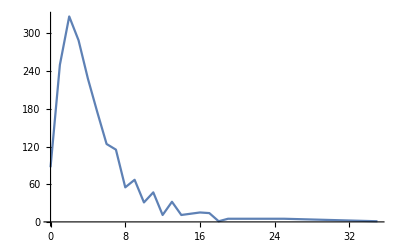

```mathematica
Tally[Table[allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]]//Sort//ListLinePlot
```